## Maryland Adjacency Matrix

```mathematica
ClearAll[type,coordg,colorsg,i,i2,edgeStyleg,vertexStyleg,g,areaa,areaaa]
```

```mathematica
Clear[generators,loads]
```

```mathematica
i= Import["Documents/Networks_Research/MDG.jpg"];
i2=ImageTake[ImageResize[i,1600],{65,999},{100,1500}]
```

-Graphics-

-Graphics-

```mathematica
coord={{193.74340527577942,653.9040767386092},{142.2278177458034,674.0623501199042},{637.2254196642687,564.3117505995203},{746.9760191846524,750.2158273381294},{746.9760191846524,734.537170263789},{746.9760191846524,691.9808153477218},{659.6235011990409,629.2661870503597},{686.5011990407675,703.1798561151079},{596.9088729016787,651.6642685851318},{621.5467625899281,707.6594724220623},{590.1894484412471,723.3381294964029},{558.832134292566,696.4604316546763},{556.5923261390888,566.5515587529976},{529.7146282973622,568.7913669064748},{545.3932853717027,577.7505995203836},{547.6330935251799,604.6282973621103},{370.68824940047966,506.0767386091127},{256.4580335731415,575.5107913669065},{337.0911270983214,564.3117505995203},{473.7194244604317,564.3117505995203},{489.39808153477225,586.7098321342926},{496.11750599520394,615.8273381294964},{534.1942446043166,676.3021582733813},{451.32134292565956,759.1750599520383},{458.04076738609115,694.220623501199},{419.96402877697847,680.7817745803357},{267.65707434052763,703.1798561151079},{131.02877697841728,712.1390887290167},{211.66187050359719,721.0983213429256},{63.834532374100746,669.5827338129496},{195.98321342925664,696.4604316546763},{247.49880095923265,714.378896882494},{240.779376498801,700.9400479616306},{218.38129496402883,573.2709832134292},{187.02398081534778,604.6282973621103},{131.02877697841728,600.1486810551559},{66.07434052757796,627.0263788968824},{935.1199040767387,698.7002398081534},{995.5947242206237,727.8177458033573},{1015.7529976019187,725.57793764988},{1183.73860911271,703.1798561151078},{1174.7793764988012,689.7410071942445},{1179.2589928057555,716.6187050359712},{1192.697841726619,736.7769784172662},{1206.1366906474823,747.9760191846522},{1150.1414868105517,678.5419664268584},{1154.6211031175062,539.6738609112709},{1212.8561151079139,559.8321342925658},{1150.1414868105517,456.80095923261376},{1123.263788968825,472.4796163069543},{1091.906474820144,472.4796163069543},{1065.0287769784175,467.9999999999999},{1044.8705035971225,420.96402877697835},{1224.0551558753,526.2350119904075},{1219.5755395683454,452.32134292565934},{1228.5347721822543,389.60671462829725},{1266.611510791367,467.9999999999999},{1152.381294964029,291.05515587529965},{1241.9736211031177,268.6570743405274},{1331.5659472422064,311.2134292565946},{1383.0815347721825,295.5347721822541},{1365.1630695443646,353.76978417266173},{1322.6067146282976,264.177458033573},{1331.5659472422064,214.90167865707417},{1380.8417266187053,241.77937649880073},{1208.3764988009593,196.98321342925647},{1277.810551558753,201.46282973621078},{1284.529976019185,170.1055155875299},{1212.8561151079139,170.1055155875299},{95.19184652278179,548.6330935251798},{608.1079136690648,396.32613908872895},{699.9400479616307,351.5299760191846},{802.9712230215829,353.76978417266173},{874.6450839328538,288.8153477218224},{955.2781774580337,257.4580335731414},{885.84412470024,459.04076738609115},{865.685851318945,459.04076738609115},{807.4508393285373,503.8369304556355},{467.0000000000001,653.9040767386092},{1020.232613908873,741.2565947242207},{1215.0959232613911,691.9808153477219},{652.9463010568409,588.8517566409597},{692.9634390174235,598.1890888317623},{732.9805769780062,602.1908026278206},{740.9840045701227,555.5041416738075},{690.2956298200513,532.8277634961439},{650.2784918594687,555.5041416738075},{648.9445872607826,544.8329048843187},{644.9428734647242,528.8260497000857},{626.268209083119,484.80719794344475},{683.6261068266209,495.47843473293347},{748.9874321622393,460.7969151670951},{786.3367609254498,518.154812910597},{786.3367609254498,479.47157954870033},{1214.5201371036844,608.8603256212509},{1085.131391031134,678.2233647529276},{1058.453299057412,692.8963153384746},{1042.446443873179,695.5641245358468},{846.3624678663238,247.37217937732078},{803.6775207083689,210.02285061411033},{813.0148528991716,282.05369894315913},{835.691231076835,358.08626106826625},{857.0337046558125,387.4321622393602},{797.0079977149385,368.75749785775497},{759.658668951728,386.0982576406741},{805.011425307055,390.0999714367324},{883.7117966295343,439.45444158811756},{879.710082833476,482.1393887460724},{950.4070265638388,430.11710939731495},{899.7186518137673,392.7677806341044},{830.3556126820907,428.78320479862884},{857.0337046558125,454.1273921736646},{830.3556126820907,490.14281633818894},{794.3401885175663,438.12053698943157},{839.6929448728933,512.8191945158526},{862.3693230505569,543.4990002856327},{786.3367609254498,387.4321622393602},{778.3333333333333,402.1051128249072},{794.3401885175663,411.44244501570984},{831.6895172807768,542.1650956869465},{935.7340759782918,507.48357612110823},{945.0714081690944,538.1633818908883},{843.6946586689517,578.180519851471},{846.3624678663238,622.199371608112},{982.4207369323049,706.2353613253355},{985.0885461296771,635.5384175949728},{1006.4310197086545,644.8757497857754},{1033.1091116823764,622.1993716081118},{1065.1228220508424,732.9134532990572},{977.0851185375607,591.5195658383318},{1121.1468151956583,732.9134532990572},{1049.1159668666094,623.5332762067978},{1009.0988289060267,600.8568980291343},{1014.4344473007711,758.257640674093},{963.7460725506996,526.1582405027133},{938.4018851756639,566.175378463296},{953.074835761211,608.8603256212509},{963.7460725506996,715.5726935161381},{923.728934590117,658.2147957726363},{943.7375035704083,615.5298486146814},{983.754641530991,570.1770922593544},{834.3285371702639,635.9856115107914},{870.1654676258994,622.5467625899281},{910.4820143884892,620.3069544364508},{890.3237410071943,602.3884892086331},{910.4820143884892,595.6690647482014},{899.2829736211033,539.673860911271},{930.6402877697842,577.7505995203837},{926.1606714628299,559.832134292566},{901.5227817745804,577.7505995203837},{912.7218225419665,564.3117505995205},{906.0023980815349,550.8729016786571},{546.6022727272726,674.9659090909092}}




colors={{50,39,37},{34,32,28},{204,220,217},{72,70,70},{205,210,212},{203,213,216},{187,110,40},{33,20,20},{201,197,200},{54,39,22},{152,146,154},{208,210,217},{199,213,210},{208,213,211},{210,208,213},{223,220,226},{21,145,77},{251,252,253},{219,221,222},{185,194,191},{217,219,220},{214,218,220},{215,232,226},{205,209,211},{198,204,205},{40,38,38},{172,181,173},{205,213,210},{207,208,211},{222,226,226},{218,223,229},{210,207,204},{170,177,178},{214,224,222},{171,171,171},{208,209,211},{217,220,219},{209,211,211},{29,31,27},{206,209,211},{169,175,182},{215,217,219},{216,220,221},{220,220,236},{208,212,209},{206,212,217},{223,223,221},{100,108,106},{212,210,212},{210,209,206},{226,228,233},{206,210,216},{35,30,35},{211,211,209},{223,219,217},{217,232,226},{211,209,208},{34,32,29},{200,198,199},{27,19,24},{218,220,223},{221,221,223},{208,222,218},{207,214,210},{183,178,188},{210,211,212},{205,211,214},{215,212,213},{204,187,150},{33,33,33},{208,215,215},{177,175,176},{236,168,104},{225,127,42},{223,58,110},{202,215,208},{60,61,82},{221,228,231},{208,213,214},{24,36,31},{10,1,5},{207,211,203},{68,74,82},{218,222,225},{206,209,206},{200,215,219},{232,228,220},{35,30,37},{38,30,27},{211,210,206},{209,212,214},{207,210,210},{197,210,216},{216,217,218},{222,224,224},{209,212,216},{214,211,209},{35,33,25},{155,167,173},{30,34,28},{203,212,208},{208,213,213},{205,215,209},{228,229,215},{39,29,31},{197,202,204},{204,213,208},{20,12,7},{211,208,212},{208,218,215},{203,206,216},{206,205,213},{203,212,214},{218,219,219},{206,212,223},{208,218,220},{208,207,214},{30,32,39},{209,211,211},{76,79,75},{35,30,31},{36,29,28},{220,226,233},{215,215,221},{207,214,216},{204,211,213},{213,210,209},{40,32,31},{205,210,212},{204,210,213},{218,209,202},{208,210,219},{215,218,215},{204,209,208},{36,29,32},{34,32,30},{206,213,211},{218,220,222},{206,213,212},{34,32,29},{32,32,29},{74,68,72},{207,205,210},{204,213,208},{210,210,212},{223,226,232},{201,209,219},{212,215,217},{167,147,115},{239,218,183},{15,15,12},{35,31,29},{30,32,37}}




Length[colors]
Length[coord]
type=Mean[#]&/@colors;
```

{{193.743,653.904},{142.228,674.062},{637.225,564.312},{746.976,750.216},{746.976,734.537},{746.976,691.981},{659.624,629.266},{686.501,703.18},{596.909,651.664},{621.547,707.659},{590.189,723.338},{558.832,696.46},{556.592,566.552},{529.715,568.791},{545.393,577.751},{547.633,604.628},{370.688,506.077},{256.458,575.511},{337.091,564.312},{473.719,564.312},{489.398,586.71},{496.118,615.827},{534.194,676.302},{451.321,759.175},{458.041,694.221},{419.964,680.782},{267.657,703.18},{131.029,712.139},{211.662,721.098},{63.8345,669.583},{195.983,696.46},{247.499,714.379},{240.779,700.94},{218.381,573.271},{187.024,604.628},{131.029,600.149},{66.0743,627.026},{935.12,698.7},{995.595,727.818},{1015.75,725.578},{1183.74,703.18},{1174.78,689.741},{1179.26,716.619},{1192.7,736.777},{1206.14,747.976},{1150.14,678.542},{1154.62,539.674},{1212.86,559.832},{1150.14,456.801},{1123.26,472.48},{1091.91,472.48},{1065.03,468.},{1044.87,420.964},{1224.06,526.235},{1219.58,452.321},{1228.53,389.607},{1266.61,468.},{1152.38,291.055},{1241.97,268.657},{1331.57,311.213},{1383.08,295.535},{1365.16,353.77},{1322.61,264.177},{1331.57,214.902},{1380.84,241.779},{1208.38,196.983},{1277.81,201.463},{1284.53,170.106},{1212.86,170.106},{95.1918,548.633},{608.108,396.326},{699.94,351.53},{802.971,353.77},{874.645,288.815},{955.278,257.458},{885.844,459.041},{865.686,459.041},{807.451,503.837},{467.,653.904},{1020.23,741.257},{1215.1,691.981},{652.946,588.852},{692.963,598.189},{732.981,602.191},{740.984,555.504},{690.296,532.828},{650.278,555.504},{648.945,544.833},{644.943,528.826},{626.268,484.807},{683.626,495.478},{748.987,460.797},{786.337,518.155},{786.337,479.472},{1214.52,608.86},{1085.13,678.223},{1058.45,692.896},{1042.45,695.564},{846.362,247.372},{803.678,210.023},{813.015,282.054},{835.691,358.086},{857.034,387.432},{797.008,368.757},{759.659,386.098},{805.011,390.1},{883.712,439.454},{879.71,482.139},{950.407,430.117},{899.719,392.768},{830.356,428.783},{857.034,454.127},{830.356,490.143},{794.34,438.121},{839.693,512.819},{862.369,543.499},{786.337,387.432},{778.333,402.105},{794.34,411.442},{831.69,542.165},{935.734,507.484},{945.071,538.163},{843.695,578.181},{846.362,622.199},{982.421,706.235},{985.089,635.538},{1006.43,644.876},{1033.11,622.199},{1065.12,732.913},{977.085,591.52},{1121.15,732.913},{1049.12,623.533},{1009.1,600.857},{1014.43,758.258},{963.746,526.158},{938.402,566.175},{953.075,608.86},{963.746,715.573},{923.729,658.215},{943.738,615.53},{983.755,570.177},{834.329,635.986},{870.165,622.547},{910.482,620.307},{890.324,602.388},{910.482,595.669},{899.283,539.674},{930.64,577.751},{926.161,559.832},{901.523,577.751},{912.722,564.312},{906.002,550.873},{546.602,674.966}}

{{50,39,37},{34,32,28},{204,220,217},{72,70,70},{205,210,212},{203,213,216},{187,110,40},{33,20,20},{201,197,200},{54,39,22},{152,146,154},{208,210,217},{199,213,210},{208,213,211},{210,208,213},{223,220,226},{21,145,77},{251,252,253},{219,221,222},{185,194,191},{217,219,220},{214,218,220},{215,232,226},{205,209,211},{198,204,205},{40,38,38},{172,181,173},{205,213,210},{207,208,211},{222,226,226},{218,223,229},{210,207,204},{170,177,178},{214,224,222},{171,171,171},{208,209,211},{217,220,219},{209,211,211},{29,31,27},{206,209,211},{169,175,182},{215,217,219},{216,220,221},{220,220,236},{208,212,209},{206,212,217},{223,223,221},{100,108,106},{212,210,212},{210,209,206},{226,228,233},{206,210,216},{35,30,35},{211,211,209},{223,219,217},{217,232,226},{211,209,208},{34,32,29},{200,198,199},{27,19,24},{218,220,223},{221,221,223},{208,222,218},{207,214,210},{183,178,188},{210,211,212},{205,211,214},{215,212,213},{204,187,150},{33,33,33},{208,215,215},{177,175,176},{236,168,104},{225,127,42},{223,58,110},{202,215,208},{60,61,82},{221,228,231},{208,213,214},{24,36,31},{10,1,5},{207,211,203},{68,74,82},{218,222,225},{206,209,206},{200,215,219},{232,228,220},{35,30,37},{38,30,27},{211,210,206},{209,212,214},{207,210,210},{197,210,216},{216,217,218},{222,224,224},{209,212,216},{214,211,209},{35,33,25},{155,167,173},{30,34,28},{203,212,208},{208,213,213},{205,215,209},{228,229,215},{39,29,31},{197,202,204},{204,213,208},{20,12,7},{211,208,212},{208,218,215},{203,206,216},{206,205,213},{203,212,214},{218,219,219},{206,212,223},{208,218,220},{208,207,214},{30,32,39},{209,211,211},{76,79,75},{35,30,31},{36,29,28},{220,226,233},{215,215,221},{207,214,216},{204,211,213},{213,210,209},{40,32,31},{205,210,212},{204,210,213},{218,209,202},{208,210,219},{215,218,215},{204,209,208},{36,29,32},{34,32,30},{206,213,211},{218,220,222},{206,213,212},{34,32,29},{32,32,29},{74,68,72},{207,205,210},{204,213,208},{210,210,212},{223,226,232},{201,209,219},{212,215,217},{167,147,115},{239,218,183},{15,15,12},{35,31,29},{30,32,37}}

153

153

```mathematica
power=0
```

0

```mathematica
Length @generators
```

0

```mathematica
generators//MatrixForm
```

generators

add refererences

```mathematica
generatorsp= For[i=1,i≤ Length@generators,i++,{power+= generators[[i,2]] ,Print[power]} ]
```

```mathematica
power
```

0

```mathematica
Dynamic@SetterBar[Dynamic@x,{1->"500kV",2->"230kV",3->"138kV",4->"115kV"},Background->connectionTypeColor[x]]
connectionTypeColor[s_]:=Dynamic@Switch[s,1,RGBColor[{0.83,0.25,0.40}],2,RGBColor[{0.99,0.56,0.14}],3,RGBColor[{0.0,0.62,0.34}],4,RGBColor[{0.17,0.44,0.71}]];

edgeList={};
DynamicModule[{p={},l={},cl={},g={}},EventHandler[Dynamic@Show[i2,g],"MouseDown":>(start=Flatten@Nearest[coord,MousePosition["Graphics"]];
sVertex=Flatten@Position[coord,start];
AppendTo[cl,start];),"MouseUp":>(end=Flatten@Nearest[coord,MousePosition["Graphics"]];
eVertex=Flatten@Position[coord,end];
AppendTo[cl,end];
AppendTo[g,Graphics[{connectionTypeColor[x],Thick,Line[Sort@cl],l},PlotRange->1,Frame->True]];
AppendTo[edgeList,Flatten@{sVertex,eVertex,x}];
cl={};)]]

Dynamic@edgeList
```

```mathematica
edgeListback={{37,2,3},{37,1,3},{37,36,3},{36,35,3},{35,34,3},{34,18,3},{18,19,3},{19,17,3},{19,20,3},{20,21,3},{20,14,3},{14,13,3},{13,15,3},{15,16,3},{16,23,3},{21,22,3},{22,23,3},{28,29,3},{30,31,3},{31,33,3},{33,32,3},{29,33,3},{32,27,3},{27,26,3},{26,25,3},{25,24,3},{13,3,3},{25,23,3},{23,12,3},{23,9,3},{12,11,3},{11,10,3},{10,8,3},{8,7,3},{8,6,3},{6,5,3},{5,4,3},{3,38,1},{38,39,1},{39,40,1},{40,41,1},{41,43,3},{43,44,3},{44,45,3},{41,42,3},{42,46,3},{42,47,3},{42,48,3},{47,49,3},{49,50,3},{50,51,3},{51,52,3},{52,53,3},{48,54,3},{54,55,3},{55,57,3},{55,56,3},{56,60,3},{60,59,3},{59,58,3},{58,66,3},{66,69,3},{66,67,3},{67,68,3},{60,63,3},{63,64,3},{63,65,3},{60,61,3},{60,62,3},{3,71,1},{71,72,1},{72,73,1},{73,74,1},{74,75,1},{3,70,1},{75,76,1},{75,76,1},{76,77,1},{77,78,1},{78,3,1},{78,38,1},{3,79,1},{79,1,1},{39,80,1},{41,81,1},{10,3,2},{10,82,2},{10,7,2},{10,7,2},{3,87,2},{87,88,2},{88,89,2},{89,90,2},{89,91,2},{89,91,2},{88,91,2},{88,91,2},{91,92,2},{91,92,2},{91,92,2},{91,92,2},{82,7,2},{82,7,2},{82,83,2},{82,83,2},{83,84,2},{82,86,2},{86,85,2},{85,84,2},{84,6,2},{83,84,2},{91,93,2},{91,93,2},{91,93,2},{91,93,2},{93,94,2},{93,94,2},{93,94,2},{93,94,2},{41,81,2},{41,44,2},{41,44,2},{41,49,2},{41,49,2},{49,58,2},{49,57,2},{57,60,2},{57,95,2},{95,81,2},{46,96,2},{96,97,2},{97,98,2},{74,99,2},{74,99,2},{99,100,2},{99,100,2},{100,101,2},{100,101,2},{100,101,2},{100,101,2},{101,102,2},{101,102,2},{101,103,2},{101,103,2},{74,103,2},{74,103,2},{74,103,2},{102,103,2},{102,103,2},{102,103,2},{102,103,2},{102,73,2},{102,73,2},{73,104,2},{73,104,2},{73,104,2},{104,105,2},{104,105,2},{103,106,2},{103,106,2},{103,106,2},{103,106,2},{76,107,4},{76,107,4},{76,108,4},{76,108,4},{76,110,4},{76,109,4},{76,109,4},{74,112,2},{103,112,2},{103,112,2},{103,112,2},{111,112,2},{111,112,2},{112,113,2},{112,113,2},{112,113,2},{112,113,2},{113,93,2},{113,93,2},{113,93,2},{113,93,2},{114,113,2},{114,113,2},{114,113,2},{114,113,2},{113,115,2},{113,115,2},{115,116,2},{115,116,2},{116,120,4},{118,92,3},{118,92,3},{104,118,2},{117,118,2},{106,118,2},{106,119,2},{106,119,2},{104,117,2},{76,121,2},{76,121,2},{121,122,2},{121,122,2},{116,123,2},{116,123,2},{123,124,2},{123,124,2},{124,38,2},{124,38,2},{122,130,2},{122,126,2},{130,126,2},{126,127,2},{126,127,2},{127,128,2},{127,128,2},{126,125,2},{38,125,2},{125,129,2},{98,129,2},{135,122,4},{135,122,4},{122,136,4},{130,137,4},{130,137,4},{133,128,4},{128,132,4},{128,132,4},{128,133,4},{39,134,4},{39,134,4},{122,137,4},{122,137,4},{122,137,4},{122,137,4},{122,137,4},{122,137,4},{97,131,2},{98,131,2},{141,137,4},{141,137,4},{137,140,4},{137,140,4},{140,139,4},{140,139,4},{137,138,4},{137,138,4},{138,80,4},{138,80,4},{123,124,4},{123,124,4},{124,142,4},{124,142,4},{124,143,4},{124,143,4},{143,144,4},{143,144,4},{144,137,4},{144,137,4},{145,144,4},{146,144,4},{146,145,4},{147,123,4},{147,123,4},{121,147,4},{121,147,4},{121,147,4},{121,147,4},{147,116,2},{137,148,4},{137,148,4},{137,148,4},{137,148,4},{148,136,4},{148,136,4},{148,149,4},{148,149,4},{148,150,4},{148,150,4},{149,151,4},{151,152,4},{152,151,4},{152,147,4},{152,147,4},{150,152,4},{150,152,4},{33,34,3},{76,115,2},{76,115,2},{41,81,1},{23,153,3},{133,130,4},{67,60,2}}
```

{{37,2,3},{37,1,3},{37,36,3},{36,35,3},{35,34,3},{34,18,3},{18,19,3},{19,17,3},{19,20,3},{20,21,3},{20,14,3},{14,13,3},{13,15,3},{15,16,3},{16,23,3},{21,22,3},{22,23,3},{28,29,3},{30,31,3},{31,33,3},{33,32,3},{29,33,3},{32,27,3},{27,26,3},{26,25,3},{25,24,3},{13,3,3},{25,23,3},{23,12,3},{23,9,3},{12,11,3},{11,10,3},{10,8,3},{8,7,3},{8,6,3},{6,5,3},{5,4,3},{3,38,1},{38,39,1},{39,40,1},{40,41,1},{41,43,3},{43,44,3},{44,45,3},{41,42,3},{42,46,3},{42,47,3},{42,48,3},{47,49,3},{49,50,3},{50,51,3},{51,52,3},{52,53,3},{48,54,3},{54,55,3},{55,57,3},{55,56,3},{56,60,3},{60,59,3},{59,58,3},{58,66,3},{66,69,3},{66,67,3},{67,68,3},{60,63,3},{63,64,3},{63,65,3},{60,61,3},{60,62,3},{3,71,1},{71,72,1},{72,73,1},{73,74,1},{74,75,1},{3,70,1},{75,76,1},{75,76,1},{76,77,1},{77,78,1},{78,3,1},{78,38,1},{3,79,1},{79,1,1},{39,80,1},{41,81,1},{10,3,2},{10,82,2},{10,7,2},{10,7,2},{3,87,2},{87,88,2},{88,89,2},{89,90,2},{89,91,2},{89,91,2},{88,91,2},{88,91,2},{91,92,2},{91,92,2},{91,92,2},{91,92,2},{82,7,2},{82,7,2},{82,83,2},{82,83,2},{83,84,2},{82,86,2},{86,85,2},{85,84,2},{84,6,2},{83,84,2},{91,93,2},{91,93,2},{91,93,2},{91,93,2},{93,94,2},{93,94,2},{93,94,2},{93,94,2},{41,81,2},{41,44,2},{41,44,2},{41,49,2},{41,49,2},{49,58,2},{49,57,2},{57,60,2},{57,95,2},{95,81,2},{46,96,2},{96,97,2},{97,98,2},{74,99,2},{74,99,2},{99,100,2},{99,100,2},{100,101,2},{100,101,2},{100,101,2},{100,101,2},{101,102,2},{101,102,2},{101,103,2},{101,103,2},{74,103,2},{74,103,2},{74,103,2},{102,103,2},{102,103,2},{102,103,2},{102,103,2},{102,73,2},{102,73,2},{73,104,2},{73,104,2},{73,104,2},{104,105,2},{104,105,2},{103,106,2},{103,106,2},{103,106,2},{103,106,2},{76,107,4},{76,107,4},{76,108,4},{76,108,4},{76,110,4},{76,109,4},{76,109,4},{74,112,2},{103,112,2},{103,112,2},{103,112,2},{111,112,2},{111,112,2},{112,113,2},{112,113,2},{112,113,2},{112,113,2},{113,93,2},{113,93,2},{113,93,2},{113,93,2},{114,113,2},{114,113,2},{114,113,2},{114,113,2},{113,115,2},{113,115,2},{115,116,2},{115,116,2},{116,120,4},{118,92,3},{118,92,3},{104,118,2},{117,118,2},{106,118,2},{106,119,2},{106,119,2},{104,117,2},{76,121,2},{76,121,2},{121,122,2},{121,122,2},{116,123,2},{116,123,2},{123,124,2},{123,124,2},{124,38,2},{124,38,2},{122,130,2},{122,126,2},{130,126,2},{126,127,2},{126,127,2},{127,128,2},{127,128,2},{126,125,2},{38,125,2},{125,129,2},{98,129,2},{135,122,4},{135,122,4},{122,136,4},{130,137,4},{130,137,4},{133,128,4},{128,132,4},{128,132,4},{128,133,4},{39,134,4},{39,134,4},{122,137,4},{122,137,4},{122,137,4},{122,137,4},{122,137,4},{122,137,4},{97,131,2},{98,131,2},{141,137,4},{141,137,4},{137,140,4},{137,140,4},{140,139,4},{140,139,4},{137,138,4},{137,138,4},{138,80,4},{138,80,4},{123,124,4},{123,124,4},{124,142,4},{124,142,4},{124,143,4},{124,143,4},{143,144,4},{143,144,4},{144,137,4},{144,137,4},{145,144,4},{146,144,4},{146,145,4},{147,123,4},{147,123,4},{121,147,4},{121,147,4},{121,147,4},{121,147,4},{147,116,2},{137,148,4},{137,148,4},{137,148,4},{137,148,4},{148,136,4},{148,136,4},{148,149,4},{148,149,4},{148,150,4},{148,150,4},{149,151,4},{151,152,4},{152,151,4},{152,147,4},{152,147,4},{150,152,4},{150,152,4},{33,34,3},{76,115,2},{76,115,2},{41,81,1},{23,153,3},{133,130,4},{67,60,2}}

```mathematica
edgeList=edgeListback
```

{{37,2,3},{37,1,3},{37,36,3},{36,35,3},{35,34,3},{34,18,3},{18,19,3},{19,17,3},{19,20,3},{20,21,3},{20,14,3},{14,13,3},{13,15,3},{15,16,3},{16,23,3},{21,22,3},{22,23,3},{28,29,3},{30,31,3},{31,33,3},{33,32,3},{29,33,3},{32,27,3},{27,26,3},{26,25,3},{25,24,3},{13,3,3},{25,23,3},{23,12,3},{23,9,3},{12,11,3},{11,10,3},{10,8,3},{8,7,3},{8,6,3},{6,5,3},{5,4,3},{3,38,1},{38,39,1},{39,40,1},{40,41,1},{41,43,3},{43,44,3},{44,45,3},{41,42,3},{42,46,3},{42,47,3},{42,48,3},{47,49,3},{49,50,3},{50,51,3},{51,52,3},{52,53,3},{48,54,3},{54,55,3},{55,57,3},{55,56,3},{56,60,3},{60,59,3},{59,58,3},{58,66,3},{66,69,3},{66,67,3},{67,68,3},{60,63,3},{63,64,3},{63,65,3},{60,61,3},{60,62,3},{3,71,1},{71,72,1},{72,73,1},{73,74,1},{74,75,1},{3,70,1},{75,76,1},{75,76,1},{76,77,1},{77,78,1},{78,3,1},{78,38,1},{3,79,1},{79,1,1},{39,80,1},{41,81,1},{10,3,2},{10,82,2},{10,7,2},{10,7,2},{3,87,2},{87,88,2},{88,89,2},{89,90,2},{89,91,2},{89,91,2},{88,91,2},{88,91,2},{91,92,2},{91,92,2},{91,92,2},{91,92,2},{82,7,2},{82,7,2},{82,83,2},{82,83,2},{83,84,2},{82,86,2},{86,85,2},{85,84,2},{84,6,2},{83,84,2},{91,93,2},{91,93,2},{91,93,2},{91,93,2},{93,94,2},{93,94,2},{93,94,2},{93,94,2},{41,81,2},{41,44,2},{41,44,2},{41,49,2},{41,49,2},{49,58,2},{49,57,2},{57,60,2},{57,95,2},{95,81,2},{46,96,2},{96,97,2},{97,98,2},{74,99,2},{74,99,2},{99,100,2},{99,100,2},{100,101,2},{100,101,2},{100,101,2},{100,101,2},{101,102,2},{101,102,2},{101,103,2},{101,103,2},{74,103,2},{74,103,2},{74,103,2},{102,103,2},{102,103,2},{102,103,2},{102,103,2},{102,73,2},{102,73,2},{73,104,2},{73,104,2},{73,104,2},{104,105,2},{104,105,2},{103,106,2},{103,106,2},{103,106,2},{103,106,2},{76,107,4},{76,107,4},{76,108,4},{76,108,4},{76,110,4},{76,109,4},{76,109,4},{74,112,2},{103,112,2},{103,112,2},{103,112,2},{111,112,2},{111,112,2},{112,113,2},{112,113,2},{112,113,2},{112,113,2},{113,93,2},{113,93,2},{113,93,2},{113,93,2},{114,113,2},{114,113,2},{114,113,2},{114,113,2},{113,115,2},{113,115,2},{115,116,2},{115,116,2},{116,120,4},{118,92,3},{118,92,3},{104,118,2},{117,118,2},{106,118,2},{106,119,2},{106,119,2},{104,117,2},{76,121,2},{76,121,2},{121,122,2},{121,122,2},{116,123,2},{116,123,2},{123,124,2},{123,124,2},{124,38,2},{124,38,2},{122,130,2},{122,126,2},{130,126,2},{126,127,2},{126,127,2},{127,128,2},{127,128,2},{126,125,2},{38,125,2},{125,129,2},{98,129,2},{135,122,4},{135,122,4},{122,136,4},{130,137,4},{130,137,4},{133,128,4},{128,132,4},{128,132,4},{128,133,4},{39,134,4},{39,134,4},{122,137,4},{122,137,4},{122,137,4},{122,137,4},{122,137,4},{122,137,4},{97,131,2},{98,131,2},{141,137,4},{141,137,4},{137,140,4},{137,140,4},{140,139,4},{140,139,4},{137,138,4},{137,138,4},{138,80,4},{138,80,4},{123,124,4},{123,124,4},{124,142,4},{124,142,4},{124,143,4},{124,143,4},{143,144,4},{143,144,4},{144,137,4},{144,137,4},{145,144,4},{146,144,4},{146,145,4},{147,123,4},{147,123,4},{121,147,4},{121,147,4},{121,147,4},{121,147,4},{147,116,2},{137,148,4},{137,148,4},{137,148,4},{137,148,4},{148,136,4},{148,136,4},{148,149,4},{148,149,4},{148,150,4},{148,150,4},{149,151,4},{151,152,4},{152,151,4},{152,147,4},{152,147,4},{150,152,4},{150,152,4},{33,34,3},{76,115,2},{76,115,2},{41,81,1},{23,153,3},{133,130,4},{67,60,2}}

```mathematica
For[y=1,y≤ Length[edgeListback],y++,If[    edgeListback[[y,1]]== 133||  edgeListback[[y,2]] ==  133   , Print[edgeListback[[y]],":"  coord[[edgeListback[[y,1]]]],":",coord[[ edgeListback[[y,2]]]],":",y] ]]
```

{133,128,4}{1009.1 :,600.857 :}:{1033.11,622.199}:227

{128,133,4}{1033.11 :,622.199 :}:{1009.1,600.857}:230

{133,130,4}{1009.1 :,600.857 :}:{977.085,591.52}:293

```mathematica
edgeStyle=#[[1]]->#[[2]]&/@Transpose[{Flatten[{#1<->#2}&@@@edgeList],connectionTypeColor[#]&/@edgeList[[All,3]]}];

vertexStyle=#[[1]]->#[[2]]&/@Transpose[{Range[Length@type],GrayLevel[#/255]&/@type}];

vlist=VertexList[Graph[Flatten[{#1<->#2}&@@@edgeList]]];

cull=Graph[Flatten[{#1<->#2}&@@@edgeList],VertexCoordinates->Table[coord[ [vlist[[i]]] ],{i,1,Length@vlist}],EdgeStyle->Flatten@{Thick,edgeStyle},VertexSize-> Large,VertexStyle->vertexStyle,EdgeWeight->edgeList[[All,3]],GridLines->Automatic]
```

-Graphics-

```mathematica
vlist
```

{37,2,1,36,35,34,18,19,17,20,21,14,13,15,16,23,22,28,29,30,31,33,32,27,26,25,24,3,12,9,11,10,8,7,6,5,4,38,39,40,41,43,44,45,42,46,47,48,49,50,51,52,53,54,55,57,56,60,59,58,66,69,67,68,63,64,65,61,62,71,72,73,74,75,70,76,77,78,79,80,81,82,87,88,89,90,91,92,83,84,86,85,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,110,109,112,111,113,114,115,116,120,118,117,119,121,122,123,124,130,126,127,128,125,129,135,136,137,133,132,134,131,141,140,139,138,142,143,144,145,146,147,148,149,150,151,152,153}

```mathematica
rcoord=Table[coord[ [vlist[[i]]] ],{i,1,Length@vlist}]
```

{{66.0743,627.026},{142.228,674.062},{193.743,653.904},{131.029,600.149},{187.024,604.628},{218.381,573.271},{256.458,575.511},{337.091,564.312},{370.688,506.077},{473.719,564.312},{489.398,586.71},{529.715,568.791},{556.592,566.552},{545.393,577.751},{547.633,604.628},{534.194,676.302},{496.118,615.827},{131.029,712.139},{211.662,721.098},{63.8345,669.583},{195.983,696.46},{240.779,700.94},{247.499,714.379},{267.657,703.18},{419.964,680.782},{458.041,694.221},{451.321,759.175},{637.225,564.312},{558.832,696.46},{596.909,651.664},{590.189,723.338},{621.547,707.659},{686.501,703.18},{659.624,629.266},{746.976,691.981},{746.976,734.537},{746.976,750.216},{935.12,698.7},{995.595,727.818},{1015.75,725.578},{1183.74,703.18},{1179.26,716.619},{1192.7,736.777},{1206.14,747.976},{1174.78,689.741},{1150.14,678.542},{1154.62,539.674},{1212.86,559.832},{1150.14,456.801},{1123.26,472.48},{1091.91,472.48},{1065.03,468.},{1044.87,420.964},{1224.06,526.235},{1219.58,452.321},{1266.61,468.},{1228.53,389.607},{1331.57,311.213},{1241.97,268.657},{1152.38,291.055},{1208.38,196.983},{1212.86,170.106},{1277.81,201.463},{1284.53,170.106},{1322.61,264.177},{1331.57,214.902},{1380.84,241.779},{1383.08,295.535},{1365.16,353.77},{608.108,396.326},{699.94,351.53},{802.971,353.77},{874.645,288.815},{955.278,257.458},{95.1918,548.633},{885.844,459.041},{865.686,459.041},{807.451,503.837},{467.,653.904},{1020.23,741.257},{1215.1,691.981},{652.946,588.852},{650.278,555.504},{648.945,544.833},{644.943,528.826},{626.268,484.807},{683.626,495.478},{748.987,460.797},{692.963,598.189},{732.981,602.191},{690.296,532.828},{740.984,555.504},{786.337,518.155},{786.337,479.472},{1214.52,608.86},{1085.13,678.223},{1058.45,692.896},{1042.45,695.564},{846.362,247.372},{803.678,210.023},{813.015,282.054},{835.691,358.086},{857.034,387.432},{797.008,368.757},{759.659,386.098},{805.011,390.1},{883.712,439.454},{879.71,482.139},{899.719,392.768},{950.407,430.117},{857.034,454.127},{830.356,428.783},{830.356,490.143},{794.34,438.121},{839.693,512.819},{862.369,543.499},{831.69,542.165},{778.333,402.105},{786.337,387.432},{794.34,411.442},{935.734,507.484},{945.071,538.163},{843.695,578.181},{846.362,622.199},{977.085,591.52},{985.089,635.538},{1006.43,644.876},{1033.11,622.199},{982.421,706.235},{1065.12,732.913},{963.746,526.158},{938.402,566.175},{953.075,608.86},{1009.1,600.857},{1049.12,623.533},{1014.43,758.258},{1121.15,732.913},{983.755,570.177},{943.738,615.53},{923.729,658.215},{963.746,715.573},{834.329,635.986},{870.165,622.547},{910.482,620.307},{890.324,602.388},{910.482,595.669},{899.283,539.674},{930.64,577.751},{926.161,559.832},{901.523,577.751},{912.722,564.312},{906.002,550.873},{546.602,674.966}}

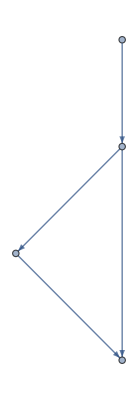

```mathematica
jabb=Graph[{4-> 3,3->2,3->1,1->2}]
```

```mathematica
AdjacencyMatrix[jabb]//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
i2
```

-Graphics-

eigenvalue spectrum, Laplacian, clustering coefficient

```mathematica
maryadj=AdjacencyMatrix[cull]
```

SparseArray[<388>, {153, 153}]

```mathematica
maryadj//MatrixForm
```

(1)
 |  |  |  |

```mathematica
mk=({{5, 4, 6}, {3, 8, 5}, {7, 8, 6}})
```

{{5,4,6},{3,8,5},{7,8,6}}

```mathematica
collp=(muu=#1;
muu[[{#2,#3}]]=muu[[{#3,#2}]];
muu[[All,{#2,#3}]]=muu[[All,{#3,#2}]])&
```

(muu=#1;muu⟦{#2,#3}⟧=muu⟦{#3,#2}⟧;muu⟦All,{#2,#3}⟧=muu⟦All,{#3,#2}⟧)&

```mathematica
collp@@{mk,1,3};
muu//MatrixForm
```

(6 | 8 | 7
5 | 8 | 3
6 | 4 | 5)

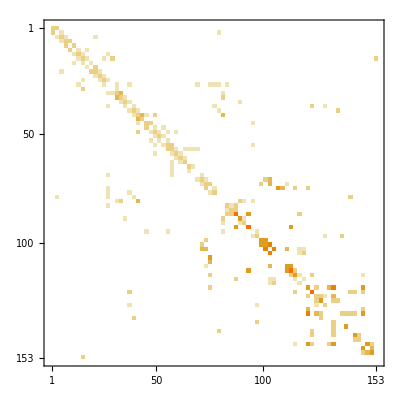

```mathematica
MatrixPlot[maryadj]
```

```mathematica
For[y=1,y≤ Length[generatz],y++,Print[Transpose[maryadj[[All,{generatz[[y]]}]]]//MatrixForm] ]
```

```mathematica
Length[generatz]
```

0

```mathematica
For[y=0,y<=Length[type],y++,If[type[[y]]<165&&type[[y]]>132,Print[type[[y]],  "  ",y ]]]
```

452/3  11

143  149

```mathematica
For[y=1,y≤ Length[generatz],y++,{maryadj[[{-y,generatz[[y]]}]] =  maryadj[[{generatz[[y]],-y}]]  ,maryadj[[All,{-y,generatz[[y]]}  ]]=maryadj[[All,{generatz[[y]],-y} ]] }  ]
```

## Generator Capacity-Vertex list

```mathematica
i2
```

-Graphics-

```mathematica
generators={{"Luke Mill",65,{142.2278177458034,674.0623501199042},2},

{"Indian River",229,{1335.392699115044,309.06157817109147},2},

{"Vienna",183,{1147.6972713864304,293.56379056047194},2},

{"Easton",69,{1046.1006637168139,424.43399705014747},2},

{"Rock Springs",770,{1044.3786873156341,696.5062684365781},2},

{"Perryman",404,{1034.0468289085543,620.7393067846607},2},

{"Sparrows Point",120,{963.4457964601768,529.4745575221239},2},

{"Riverside",244,{947.9480088495573,539.8064159292035},2},

{"Gould Street",104,{904.8985988200589,550.1382743362832},2},

{"Brandon Shores + H.A. Wagner",2429,{934.1721976401179,510.5328171091445},2},

{"Philadelphia Road",83,{937.6161504424776,565.6360619469026},2},

{"Notch Cliff",144,{939.3381268436576,615.5733775811209},2},

{"R.P. Smith",110,{545.0055309734512,675.8425516224189},2},

{"Dickerson",930,{648.3241150442477,544.9723451327434},2},

{"Montgomery County RRF",68,{643.1581858407078,527.7525811209439},2},

{"Mt. Storm",1600,{93.84771386430677,553.582227138643},2},

{"Buzzard Point",256,{777.4723451327432,405.49225663716817},2},

{"Potomac River",514,{756.8086283185839,386.5505162241888},2},

{"Chalk Point",2563,{875.625,286.6758849557523},2},

{"Calvert Hills",1829,{958.2798672566371,257.4022861356932},75},

{"Morgantown",1548,{801.5800147492625,210.90892330383485},2},

{"C.P. Crane",56,{982.3875368731563,572.5239675516224},2},

{"Peach Bottom",1160,{994.4413716814158,730.945796460177},2},

{"Muddy Run",800,{1021.9929941002947,744.7216076696164},2},

     {"Warrior Run",229,{240.21283171478316,703.1423972144268},2},

{"Panda Brandywine",289,{856.756313131313,387.21843434343447},2},

{"Exelon Conowingo",572,{1086.7184343434344,678.503787878788},2}
}
```

{{Luke Mill,65,{142.228,674.062},2},{Indian River,229,{1335.39,309.062},2},{Vienna,183,{1147.7,293.564},2},{Easton,69,{1046.1,424.434},2},{Rock Springs,770,{1044.38,696.506},2},{Perryman,404,{1034.05,620.739},2},{Sparrows Point,120,{963.446,529.475},2},{Riverside,244,{947.948,539.806},2},{Gould Street,104,{904.899,550.138},2},{Brandon Shores + H.A. Wagner,2429,{934.172,510.533},2},{Philadelphia Road,83,{937.616,565.636},2},{Notch Cliff,144,{939.338,615.573},2},{R.P. Smith,110,{545.006,675.843},2},{Dickerson,930,{648.324,544.972},2},{Montgomery County RRF,68,{643.158,527.753},2},{Mt. Storm,1600,{93.8477,553.582},2},{Buzzard Point,256,{777.472,405.492},2},{Potomac River,514,{756.809,386.551},2},{Chalk Point,2563,{875.625,286.676},2},{Calvert Hills,1829,{958.28,257.402},75},{Morgantown,1548,{801.58,210.909},2},{C.P. Crane,56,{982.388,572.524},2},{Peach Bottom,1160,{994.441,730.946},2},{Muddy Run,800,{1021.99,744.722},2},{Warrior Run,229,{240.213,703.142},2},{Panda Brandywine,289,{856.756,387.218},2},{Exelon Conowingo,572,{1086.72,678.504},2}}

```mathematica
generators//MatrixForm
```

(Luke Mill | 65 | {142.228,674.062} | 2
Indian River | 229 | {1335.39,309.062} | 2
Vienna | 183 | {1147.7,293.564} | 2
Easton | 69 | {1046.1,424.434} | 2
Rock Springs | 770 | {1044.38,696.506} | 2
Perryman | 404 | {1034.05,620.739} | 2
Sparrows Point | 120 | {963.446,529.475} | 2
Riverside | 244 | {947.948,539.806} | 2
Gould Street | 104 | {904.899,550.138} | 2
Brandon Shores + H.A. Wagner | 2429 | {934.172,510.533} | 2
Philadelphia Road | 83 | {937.616,565.636} | 2
Notch Cliff | 144 | {939.338,615.573} | 2
R.P. Smith | 110 | {545.006,675.843} | 2
Dickerson | 930 | {648.324,544.972} | 2
Montgomery County RRF | 68 | {643.158,527.753} | 2
Mt. Storm | 1600 | {93.8477,553.582} | 2
Buzzard Point | 256 | {777.472,405.492} | 2
Potomac River | 514 | {756.809,386.551} | 2
Chalk Point | 2563 | {875.625,286.676} | 2
Calvert Hills | 1829 | {958.28,257.402} | 75
Morgantown | 1548 | {801.58,210.909} | 2
C.P. Crane | 56 | {982.388,572.524} | 2
Peach Bottom | 1160 | {994.441,730.946} | 2
Muddy Run | 800 | {1021.99,744.722} | 2
Warrior Run | 229 | {240.213,703.142} | 2
Panda Brandywine | 289 | {856.756,387.218} | 2
Exelon Conowingo | 572 | {1086.72,678.504} | 2)

```mathematica
generators[[3,3]]
```

{1147.7,293.564}

```mathematica
Flatten@Position[rcoord,Flatten@Nearest[rcoord,generators[[#,3]]  ]]&/@ Table[i,{i,Length@generators}]
```

{{2},{58},{60},{53},{98},{128},{131},{122},{152},{121},{132},{139},{153},{84},{85},{75},{118},{105},{73},{74},{100},{138},{39},{80},{22},{103},{96}}

```mathematica
genind=Flatten[{{2},{22},{39},{53},{60},{58},{75},{73},{74},{80},{84},{85},{96},{98},{100},{103},{105},{118},{121},{122},{128},{131},{132},{139},{138},{152},{153}}]
```

{2,22,39,53,60,58,75,73,74,80,84,85,96,98,100,103,105,118,121,122,128,131,132,139,138,152,153}

```mathematica
genind
```

{2,22,39,53,60,58,75,73,74,80,84,85,96,98,100,103,105,118,121,122,128,131,132,139,138,152,153}

```mathematica
Reverse@Sort@genind
```

{153,152,139,138,132,131,128,122,121,118,105,103,100,98,96,85,84,80,75,74,73,60,58,53,39,22,2}

```mathematica
repgin=(generators[[#1,4]]=#2 )&
```

(generators⟦#1,4⟧=#2)&

```mathematica
MapThread[repgin,{Table[i,{i,Length@generators}],genind}]
```

{2,22,39,53,60,58,75,73,74,80,84,85,96,98,100,103,105,118,121,122,128,131,132,139,138,152,153}

```mathematica
pend=
(muu[[{#1,#2}]]=muu[[{#2,#1}]];
muu[[All,{#1,#2}]]=muu[[All,{#2,#1}]];)&
```

(muu⟦{#1,#2}⟧=muu⟦{#2,#1}⟧;muu⟦All,{#1,#2}⟧=muu⟦All,{#2,#1}⟧;)&

```mathematica
muu=maryadj;
MapThread[pend,{Table[154-i,{i,Length@genind}],Reverse@Sort@genind}];
muu//MatrixForm
```

(1)
 |  |  |  |

```mathematica
generators=SortBy[generators,Last]
```

{{Luke Mill,65,{142.228,674.062},2},{Indian River,229,{1335.39,309.062},22},{Vienna,183,{1147.7,293.564},39},{Easton,69,{1046.1,424.434},53},{Perryman,404,{1034.05,620.739},58},{Rock Springs,770,{1044.38,696.506},60},{Riverside,244,{947.948,539.806},73},{Gould Street,104,{904.899,550.138},74},{Sparrows Point,120,{963.446,529.475},75},{Brandon Shores + H.A. Wagner,2429,{934.172,510.533},80},{Philadelphia Road,83,{937.616,565.636},84},{Notch Cliff,144,{939.338,615.573},85},{R.P. Smith,110,{545.006,675.843},96},{Dickerson,930,{648.324,544.972},98},{Montgomery County RRF,68,{643.158,527.753},100},{Mt. Storm,1600,{93.8477,553.582},103},{Buzzard Point,256,{777.472,405.492},105},{Potomac River,514,{756.809,386.551},118},{Chalk Point,2563,{875.625,286.676},121},{Calvert Hills,1829,{958.28,257.402},122},{Morgantown,1548,{801.58,210.909},128},{C.P. Crane,56,{982.388,572.524},131},{Peach Bottom,1160,{994.441,730.946},132},{Warrior Run,229,{240.213,703.142},138},{Muddy Run,800,{1021.99,744.722},139},{Panda Brandywine,289,{856.756,387.218},152},{Exelon Conowingo,572,{1086.72,678.504},153}}

```mathematica
generators//MatrixForm
```

(Luke Mill | 65 | {142.228,674.062} | 2
Indian River | 229 | {1335.39,309.062} | 22
Vienna | 183 | {1147.7,293.564} | 39
Easton | 69 | {1046.1,424.434} | 53
Perryman | 404 | {1034.05,620.739} | 58
Rock Springs | 770 | {1044.38,696.506} | 60
Riverside | 244 | {947.948,539.806} | 73
Gould Street | 104 | {904.899,550.138} | 74
Sparrows Point | 120 | {963.446,529.475} | 75
Brandon Shores + H.A. Wagner | 2429 | {934.172,510.533} | 80
Philadelphia Road | 83 | {937.616,565.636} | 84
Notch Cliff | 144 | {939.338,615.573} | 85
R.P. Smith | 110 | {545.006,675.843} | 96
Dickerson | 930 | {648.324,544.972} | 98
Montgomery County RRF | 68 | {643.158,527.753} | 100
Mt. Storm | 1600 | {93.8477,553.582} | 103
Buzzard Point | 256 | {777.472,405.492} | 105
Potomac River | 514 | {756.809,386.551} | 118
Chalk Point | 2563 | {875.625,286.676} | 121
Calvert Hills | 1829 | {958.28,257.402} | 122
Morgantown | 1548 | {801.58,210.909} | 128
C.P. Crane | 56 | {982.388,572.524} | 131
Peach Bottom | 1160 | {994.441,730.946} | 132
Warrior Run | 229 | {240.213,703.142} | 138
Muddy Run | 800 | {1021.99,744.722} | 139
Panda Brandywine | 289 | {856.756,387.218} | 152
Exelon Conowingo | 572 | {1086.72,678.504} | 153)

```mathematica
repgin
```

(generators⟦#1,4⟧=#2)&

```mathematica
l=Partition[Riffle[Reverse@Sort@genind,Table[154-i,{i,Length@genind}]],2]
```

{{153,153},{152,152},{139,151},{138,150},{132,149},{131,148},{128,147},{122,146},{121,145},{118,144},{105,143},{103,142},{100,141},{98,140},{96,139},{85,138},{84,137},{80,136},{75,135},{74,134},{73,133},{60,132},{58,131},{53,130},{39,129},{22,128},{2,127}}

```mathematica
k={};
For[i=1,i<=Length@l,i++,AppendTo[k,DeleteDuplicates[l[[i ]] ]]    ]
```

```mathematica
k
```

{{153},{152},{139,151},{138,150},{132,149},{131,148},{128,147},{122,146},{121,145},{118,144},{105,143},{103,142},{100,141},{98,140},{96,139},{85,138},{84,137},{80,136},{75,135},{74,134},{73,133},{60,132},{58,131},{53,130},{39,129},{22,128},{2,127}}

```mathematica
ll=Table[i,{i,153}]
For[i=1,i≤ Length@k,i++,ll=Permute[ll,Cycles[{k[[i]]}      ]]];
ll
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153}

{1,127,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,147,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,129,40,41,42,43,44,45,46,47,48,49,50,51,52,130,54,55,56,57,148,59,149,61,62,63,64,65,66,67,68,69,70,71,72,133,134,135,76,77,78,79,136,81,82,83,137,150,86,87,88,89,90,91,92,93,94,95,151,97,140,99,141,101,102,142,104,143,106,107,108,109,110,111,112,113,114,115,116,117,144,119,120,145,146,123,124,125,126,2,22,39,53,58,60,73,74,75,80,84,85,96,98,100,103,105,118,121,122,128,131,132,138,139,152,153}

```mathematica
Sort@genind
```

{2,22,39,53,58,60,73,74,75,80,84,85,96,98,100,103,105,118,121,122,128,131,132,138,139,152,153}

```mathematica
Length@genind
```

27

```mathematica
coord1=rcoord;
For[i=1,i≤ Length@k,i++,coord1=Permute[coord1,Cycles[{k[[i]]}]    ]  ];
coord1[[139]]
rcoord[[96]]
```

{1085.13,678.223}

{1085.13,678.223}

```mathematica
MapThread[repgin,{Table[i,{i,Length@genind}],Table[126+i,{i,Length@genind}] }   ]
```

{127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153}

```mathematica
generators//MatrixForm
muu//MatrixForm
coord1
```

(Luke Mill | 65 | {142.228,674.062} | 127
Indian River | 229 | {1335.39,309.062} | 128
Vienna | 183 | {1147.7,293.564} | 129
Easton | 69 | {1046.1,424.434} | 130
Perryman | 404 | {1034.05,620.739} | 131
Rock Springs | 770 | {1044.38,696.506} | 132
Riverside | 244 | {947.948,539.806} | 133
Gould Street | 104 | {904.899,550.138} | 134
Sparrows Point | 120 | {963.446,529.475} | 135
Brandon Shores + H.A. Wagner | 2429 | {934.172,510.533} | 136
Philadelphia Road | 83 | {937.616,565.636} | 137
Notch Cliff | 144 | {939.338,615.573} | 138
R.P. Smith | 110 | {545.006,675.843} | 139
Dickerson | 930 | {648.324,544.972} | 140
Montgomery County RRF | 68 | {643.158,527.753} | 141
Mt. Storm | 1600 | {93.8477,553.582} | 142
Buzzard Point | 256 | {777.472,405.492} | 143
Potomac River | 514 | {756.809,386.551} | 144
Chalk Point | 2563 | {875.625,286.676} | 145
Calvert Hills | 1829 | {958.28,257.402} | 146
Morgantown | 1548 | {801.58,210.909} | 147
C.P. Crane | 56 | {982.388,572.524} | 148
Peach Bottom | 1160 | {994.441,730.946} | 149
Warrior Run | 229 | {240.213,703.142} | 150
Muddy Run | 800 | {1021.99,744.722} | 151
Panda Brandywine | 289 | {856.756,387.218} | 152
Exelon Conowingo | 572 | {1086.72,678.504} | 153)

(1)
 |  |  |  |

{{66.0743,627.026},{1006.43,644.876},{193.743,653.904},{131.029,600.149},{187.024,604.628},{218.381,573.271},{256.458,575.511},{337.091,564.312},{370.688,506.077},{473.719,564.312},{489.398,586.71},{529.715,568.791},{556.592,566.552},{545.393,577.751},{547.633,604.628},{534.194,676.302},{496.118,615.827},{131.029,712.139},{211.662,721.098},{63.8345,669.583},{195.983,696.46},{899.283,539.674},{247.499,714.379},{267.657,703.18},{419.964,680.782},{458.041,694.221},{451.321,759.175},{637.225,564.312},{558.832,696.46},{596.909,651.664},{590.189,723.338},{621.547,707.659},{686.501,703.18},{659.624,629.266},{746.976,691.981},{746.976,734.537},{746.976,750.216},{935.12,698.7},{982.421,706.235},{1015.75,725.578},{1183.74,703.18},{1179.26,716.619},{1192.7,736.777},{1206.14,747.976},{1174.78,689.741},{1150.14,678.542},{1154.62,539.674},{1212.86,559.832},{1150.14,456.801},{1123.26,472.48},{1091.91,472.48},{1065.03,468.},{1065.12,732.913},{1224.06,526.235},{1219.58,452.321},{1266.61,468.},{1228.53,389.607},{930.64,577.751},{1241.97,268.657},{926.161,559.832},{1208.38,196.983},{1212.86,170.106},{1277.81,201.463},{1284.53,170.106},{1322.61,264.177},{1331.57,214.902},{1380.84,241.779},{1383.08,295.535},{1365.16,353.77},{608.108,396.326},{699.94,351.53},{802.971,353.77},{953.075,608.86},{1009.1,600.857},{1049.12,623.533},{885.844,459.041},{865.686,459.041},{807.451,503.837},{467.,653.904},{1014.43,758.258},{1215.1,691.981},{652.946,588.852},{650.278,555.504},{1121.15,732.913},{901.523,577.751},{626.268,484.807},{683.626,495.478},{748.987,460.797},{692.963,598.189},{732.981,602.191},{690.296,532.828},{740.984,555.504},{786.337,518.155},{786.337,479.472},{1214.52,608.86},{912.722,564.312},{1058.45,692.896},{923.729,658.215},{846.362,247.372},{963.746,715.573},{813.015,282.054},{835.691,358.086},{834.329,635.986},{797.008,368.757},{870.165,622.547},{805.011,390.1},{883.712,439.454},{879.71,482.139},{899.719,392.768},{950.407,430.117},{857.034,454.127},{830.356,428.783},{830.356,490.143},{794.34,438.121},{839.693,512.819},{862.369,543.499},{831.69,542.165},{910.482,620.307},{786.337,387.432},{794.34,411.442},{890.324,602.388},{910.482,595.669},{843.695,578.181},{846.362,622.199},{977.085,591.52},{985.089,635.538},{142.228,674.062},{240.779,700.94},{995.595,727.818},{1044.87,420.964},{1331.57,311.213},{1152.38,291.055},{874.645,288.815},{955.278,257.458},{95.1918,548.633},{1020.23,741.257},{648.945,544.833},{644.943,528.826},{1085.13,678.223},{1042.45,695.564},{803.678,210.023},{857.034,387.432},{759.659,386.098},{778.333,402.105},{935.734,507.484},{945.071,538.163},{1033.11,622.199},{963.746,526.158},{938.402,566.175},{983.755,570.177},{943.738,615.53},{906.002,550.873},{546.602,674.966}}

## Calculations using Adjacency Matrix

eigenvalue spectrum, Laplacian, clustering coefficient

```mathematica
fmuu={{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,1,2,0},{0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,2,0},{0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,3,0,0,0,0,2,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,2,1,1,0,1,0,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,3,0,0,1,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,2,0,0,1,2,0,1,0,0,0,0,1,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,3,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,3,0,0,1,2,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,2,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,1,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,3,2,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,3,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,1,2,0},{0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,2,0},{0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,3,0,0,0,0,2,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,2,1,1,0,1,0,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,3,0,0,1,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,2,0,0,1,2,0,1,0,0,0,0,1,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,3,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,3,0,0,1,2,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,2,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,1,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,3,2,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,3,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
```

{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,1,2,0},{0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,2,0},{0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,3,0,0,0,0,2,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,2,1,1,0,1,0,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,3,0,0,1,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,2,0,0,1,2,0,1,0,0,0,0,1,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,3,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,3,0,0,1,2,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,2,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,1,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,3,2,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,3,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,1,2,0},{0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,2,0},{0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,3,0,0,0,0,2,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,2,1,1,0,1,0,1,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,3,0,0,1,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,2,0,0,1,2,0,1,0,0,0,0,1,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,3,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,3,0,0,1,2,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,2,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,1,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,1,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,3,2,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,3,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,1,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
fscoord1=15.26*{{0.19947857,1.30165},{0.33934571,1.3469929},{0.34000571,1.4939714},{0.53570571,1.4830286},{0.60174571,1.2914871},{0.73211571,1.5057},{0.79155857,1.4830286},{0.72058857,1.34543},{0.75465,1.3563743},{0.80248143,1.3657557},{0.79887286,1.3313571},{0.73948286,1.2320729},{0.67936143,1.1460771},{0.85331429,1.1437329},{0.71998714,1.0624286},{0.78161143,1.0225571},{0.79102571,1.04132},{0.82147286,1.0288114},{0.84393429,1.0444471},{0.62577571,1.0319386},{0.77437143,1.0037957},{0.82439286,0.98190571},{0.89759714,0.97956},{0.91716714,0.97956},{0.91719857,0.90841857},{0.69973714,0.95767143},{0.59465571,0.92561857},{0.63017714,0.91232857},{0.70337571,0.92483571},{0.59177714,0.87871143},{0.73454714,0.91232857},{0.76861286,0.91232857},{0.78892143,0.88027571},{0.74039286,0.80522571},{0.62442571,0.80288},{0.93174143,0.79897143},{0.64692286,0.73721143},{0.7194,0.74424714},{0.70057714,0.69421286},{0.96367,0.71219429},{0.93252714,0.65981571},{0.96586714,0.66059714},{0.98255286,0.62385429},{0.74264143,0.63245286},{0.74194714,0.56209429},{0.94851286,0.56678429},{0.97967857,0.56678429},{0.89126714,0.53629571},{0.91955571,0.48626286},{0.90144429,0.46437286},{0.98334714,0.46359143},{0.92464429,0.4503},{0.90508571,0.42450286},{0.78152571,1.2195643},{0.82580286,1.07181},{0.63383429,0.83493286},{0.92017857,0.72157571},{0.71146429,0.65825143},{0.96230143,0.52691429},{0.99128857,0.53473143},{0.95364714,0.42606571},{0.94931,0.39870429},{0.68789143,1.5322714},{0.59892857,1.1015171},{0.96435571,0.80131571},{0.91715857,0.99910429},{0.99339571,0.69030429},{0.34149429,1.4064086},{0.53646857,1.3946814},{0.7887,1.3907729},{0.73145286,1.3641929},{0.79028,1.0882271},{0.85700143,0.99832286},{0.80411143,0.95141714},{0.82440571,0.95141714},{0.64685714,0.89043857},{0.73453429,0.94281714},{0.71934857,0.86229429},{0.74834,0.86229429},{0.71936143,0.83180571},{0.63309857,0.86229429},{0.75759286,1.2547443},{0.77928429,1.3759186},{0.74732429,1.5338429}}
```

{{3.04404,19.8632},{5.17842,20.5551},{5.18849,22.798},{8.17487,22.631},{9.18264,19.7081},{11.1721,22.977},{12.0792,22.631},{10.9962,20.5313},{11.516,20.6983},{12.2459,20.8414},{12.1908,20.3165},{11.2845,18.8014},{10.3671,17.4891},{13.0216,17.4534},{10.987,16.2127},{11.9274,15.6042},{12.0711,15.8905},{12.5357,15.6997},{12.8784,15.9383},{9.54934,15.7474},{11.8169,15.3179},{12.5802,14.9839},{13.6973,14.9481},{13.996,14.9481},{13.9965,13.8625},{10.678,14.6141},{9.07445,14.1249},{9.6165,13.9221},{10.7335,14.113},{9.03052,13.4091},{11.2092,13.9221},{11.729,13.9221},{12.0389,13.433},{11.2984,12.2877},{9.52874,12.2519},{14.2184,12.1923},{9.87204,11.2498},{10.978,11.3572},{10.6908,10.5937},{14.7056,10.8681},{14.2304,10.0688},{14.7391,10.0807},{14.9938,9.52002},{11.3327,9.65123},{11.3221,8.57756},{14.4743,8.64913},{14.9499,8.64913},{13.6007,8.18387},{14.0324,7.42037},{13.756,7.08633},{15.0059,7.07441},{14.1101,6.87158},{13.8116,6.47791},{11.9261,18.6106},{12.6018,16.3558},{9.67231,12.7411},{14.0419,11.0112},{10.8569,10.0449},{14.6847,8.04071},{15.1271,8.16},{14.5527,6.50176},{14.4865,6.08423},{10.4972,23.3825},{9.13965,16.8092},{14.7161,12.2281},{13.9958,15.2463},{15.1592,10.534},{5.2112,21.4618},{8.18651,21.2828},{12.0356,21.2232},{11.162,20.8176},{12.0597,16.6063},{13.0778,15.2344},{12.2707,14.5186},{12.5804,14.5186},{9.87104,13.5881},{11.209,14.3874},{10.9773,13.1586},{11.4197,13.1586},{10.9775,12.6934},{9.66108,13.1586},{11.5609,19.1474},{11.8919,20.9965},{11.4042,23.4064}}

```mathematica
edgecnt=0; 
For[i=1,i≤ Length@fscoord1,i++,edgecnt+= Total[fmuu[[i]] ]]
edgecnt/2
```

200

```mathematica
Vertices =84;
ng=31;
nl=53; 
degreesum=0; 
degreesumg=0; 
degreesuml=0;
For[i=1,i≤84,i++, degreesum+= Total[fmuu[[i]]]]; 
degreesum; 
edges=degreesum/2
kk=degreesum/Vertices //N
For[i=1,i≤53,i++, degreesuml+= Total[fmuu[[i]]]]; 
For[i=54,i≤84,i++, degreesumg+= Total[fmuu[[i]]]]; 
kg=degreesumg/ng //N
kl= degreesuml/nl //N
```

200

4.7619

4.48387

4.92453

```mathematica
avlength=0; 
edgecnt=0; 
For[i=1,i≤ 84,i++, If[  fmuu[[#,i]]>0,{ edgecnt+= fmuu[[#,i]]  ,avlength += fmuu[[#,i]]*EuclideanDistance[fscoord1[[#]],fscoord1[[i]]  ]}]]  &/@Table[y,{y,84}];
avlength/edgecnt
edgecnt
```

1.09314

400

```mathematica
avlengthgl=0; 
edgecntgl=0; 
For[i=1,i≤ 53,i++, { edgecntgl+= fmuu[[#,i]],(*Print[  i,"  ", #,"   ", EuclideanDistance[scoord1[[#]],scoord1[[i]] ]]   ,*)avlengthgl +=    fmuu[[#,i]]*( EuclideanDistance[fscoord1[[#]],fscoord1[[i]] ])}   ]   &/@Table[y,{y,54,84}];
avlengthgl/edgecntgl
edgecntgl
```

1.02288

105

```mathematica
avlengthgg=0; 
edgecntgg=0; 
For[i=54,i≤ 84,i++, { edgecntgg+= fmuu[[#,i]],(*Print[  i,"  ", #,"   ", EuclideanDistance[scoord1[[#]],scoord1[[i]] ]]   ,*)avlengthgg +=    fmuu[[#,i]]*( EuclideanDistance[fscoord1[[#]],fscoord1[[i]] ])}    ] &/@Table[y,{y,54,84}];
avlengthgg/edgecntgg
edgecntgg
```

0.710292

34

```mathematica
avlengthll=0; 
edgecntll=0; 
For[i=1,i≤ 53,i++, { edgecntll+= fmuu[[#,i]],(*Print[  i,"  ", #,"   ", EuclideanDistance[scoord1[[#]],scoord1[[i]] ]]   ,*)avlengthll +=    fmuu[[#,i]]*( EuclideanDistance[fscoord1[[#]],fscoord1[[i]] ])}    ] &/@Table[y,{y,1,53}];
avlengthll/edgecntll
edgecntll
```

1.27115

156

```mathematica
edgecntgg/edgecnt  //N
```

0.085

```mathematica
fwmuu=fmuu;
For[i=1,i≤ 84,i++, If[#≠ i,fwmuu[[i,#]]=fmuu[[i,#]]/(EuclideanDistance[fscoord1[[#]],fscoord1[[i]] ])    ]    ] &/@Table[y,{y,1,84}];
```

```mathematica
R=0;
Rgg=0; 
Rlg=0; 
Rll=0; 
For[i=1,i≤ 84,i++, If[fwmuu[[#,i]] ≠ 0,R+=1/fwmuu[[#,i]]    ]    ] &/@Table[y,{y,1,84}];
For[i=54,i≤ 84,i++, If[fwmuu[[#,i]] ≠ 0,Rgg+=1/fwmuu[[#,i]]     ]] &/@Table[y,{y,54,84}];
For[i=1,i≤ 53,i++, If[fwmuu[[#,i]] ≠ 0,Rlg+=1/fwmuu[[#,i]]    ]    ] &/@Table[y,{y,54,84}];
For[i=1,i≤ 53,i++, If[fwmuu[[#,i]] > 0,Rll+=1/fwmuu[[#,i]]    ]    ] &/@Table[y,{y,1,53}];
Rgg
Rlg
Rll
R/2
```

13.774

68.1873

130.212

140.18

```mathematica
lledges=0; 
For[i=1,i≤ 53,i++, If[fmuu[[#,i]] > 0,lledges+=Sign[fmuu[[#,i]] ]  ]    ] &/@Table[y,{y,1,53}];
lledges
108
lgedges=0; 
For[i=1,i≤ 53,i++, If[fmuu[[#,i]] > 0,lgedges+=Sign[fmuu[[#,i]] ]  ]    ] &/@Table[y,{y,54,84}];
lgedges
ggedges=0; 
For[i=54,i≤ 84,i++, If[fmuu[[#,i]] > 0,ggedges+=Sign[fmuu[[#,i]] ]  ]    ] &/@Table[y,{y,54,84}];
ggedges
```

108

108

71

24

```mathematica
famuu= fmuu;
For[i=1,i≤ 84,i++, famuu[[i,#]]=Sign[fmuu[[i,#]]  ]     ] &/@Table[y,{y,1,84}];
```

```mathematica
edgess=0; 
liness=0; 
For[j=1,j≤  84,j++,If[Total[famuu[[j]]]==1,edgess++]]
edgess
```

11

```mathematica
84-11
```

73

```mathematica
ki =0; 
si =0 ; 
clusteringi = 0;
For[j=1,j≤  84,j++,{ki = Total[famuu[[#]]],si  = Total[fwmuu[[#]]],If[ki>1,For[h=1,h≤ 84,h++,clusteringi +=(.5)/(si(ki-1))*(fwmuu[[#,h]]+fwmuu[[#,j]])* famuu[[#,h]]*famuu[[#,j]]*famuu[[h,j]] ]]}]&/@Table[y,{y,1,84}];
clusteringi/73
```

0.21266

```mathematica
0.18481201482730175*84/73
```

0.21266

```mathematica
200-137
```

63

```mathematica
values ={{"  ","MFLG","FLG"},{"nodes",84,84},{"number ofgenerators",ng,31},{"number ofloads",nl,53},{"power lines",edgecnt/2,200},{"<k>",kk,4.76},{"<k_g>",kg,4.48},{"<k_l>",kl,4.93},{"<ℓ>",avlength/edgecnt,1.09},{"<ℓ_gg>",avlengthgg/edgecntgg,0.71},{"<ℓ_gl>",avlengthgl/edgecntgl,1.02},{"<ℓ_ll>",avlengthll/edgecntll,1.27},{"e_gg",edgecntgg/edgecnt,0.085},{"e_gl",edgecntgl/edgecnt,0.2625},{"e_ll",edgecntll/edgecnt,0.39},{"<R_gg>",Rgg/ggedges,0.57},{"<R_gl>",Rlg/lgedges,0.96},{"<R_ll>",Rll/lledges,1.20},{"R",R/2,139.78},{"<C^ω>",clusteringi/73,0.21},{"<M_ex>",63,63},{"<d_B>","",1.37}}//N
```

{{  ,MFLG,FLG},{nodes,84.,84.},{number ofgenerators,31.,31.},{number ofloads,53.,53.},{power lines,200.,200.},{<k>,4.7619,4.76},{<k_g>,4.48387,4.48},{<k_l>,4.92453,4.93},{<ℓ>,1.09314,1.09},{<ℓ_gg>,0.710292,0.71},{<ℓ_gl>,1.02288,1.02},{<ℓ_ll>,1.27115,1.27},{e_gg,0.085,0.085},{e_gl,0.2625,0.2625},{e_ll,0.39,0.39},{<R_gg>,0.573918,0.57},{<R_gl>,0.960384,0.96},{<R_ll>,1.20567,1.2},{R,140.18,139.78},{<C^ω>,0.184812,0.21},{<M_ex>,63.,63.},{<d_B>,,1.37}}

```mathematica
TableForm[values]
```

| MFLG | FLG
nodes | 84. | 84.
number ofgenerators | 31. | 31.
number ofloads | 53. | 53.
power lines | 200. | 200.
<k> | 4.7619 | 4.76
<k_g> | 4.48387 | 4.48
<k_l> | 4.92453 | 4.93
<ℓ> | 1.09314 | 1.09
<ℓ_gg> | 0.710292 | 0.71
<ℓ_gl> | 1.02288 | 1.02
<ℓ_ll> | 1.27115 | 1.27
e_gg | 0.085 | 0.085
e_gl | 0.2625 | 0.2625
e_ll | 0.39 | 0.39
<R_gg> | 0.573918 | 0.57
<R_gl> | 0.960384 | 0.96
<R_ll> | 1.20567 | 1.2
R | 140.18 | 139.78
<C^ω> | 0.184812 | 0.21
<M_ex> | 63. | 63.
<d_B> |  | 1.37

```mathematica
EuclideanDistance[{0,0},{0,4}]
```

4

```mathematica
Vertices =153;
ng=27;
nl=126; 
degreesum=0; 
degreesumg=0; 
degreesuml=0;
For[i=1,i≤153,i++, degreesum+= Total[muu[[i]]]]; 
degreesum; 
edges=degreesum/2
kk=degreesum/Vertices //N
For[i=1,i≤126,i++, degreesuml+= Total[muu[[i]]]]; 
For[i=127,i≤153,i++, degreesumg+= Total[muu[[i]]]]; 
kg=degreesumg/ng //N
kl= degreesuml/nl //N
```

294

3.84314

4.55556

3.69048

```mathematica
?Polygon
```

RowBox[{"Polygon", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["p", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"], ",", SubscriptBox[StyleBox["p", "TI"], StyleBox["n", "TI"]]}], "}"}], "]"}] represents a filled polygon with points SubscriptBox[StyleBox["p", "TI"], StyleBox["i", "TI"]].
RowBox[{"Polygon", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["p", "TI"], StyleBox["11", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["p", "TI"], StyleBox["21", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a collection of polygons.

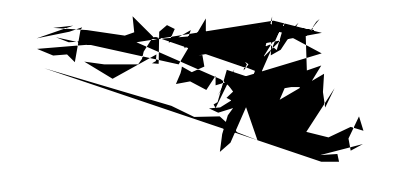

```mathematica
Graphics[Polygon[coord]]
```

```mathematica
cull
```

-Graphics-

```mathematica
i2
```

-Graphics-

```mathematica
are1={{372.06691919191917,496.89267676767685},{552.4987373737373,559.3952020202021},{636.2285353535353,555.8573232323233},{620.8977272727273,488.6376262626263},{605.5669191919192,393.1148989898991},{697.5517676767677,341.22601010101016},{803.6881313131313,344.76388888888897},{808.405303030303,283.44065656565664},{804.8674242424242,205.60732323232332},{881.5214646464646,279.9027777777778},{961.7133838383837,253.95833333333348},{949.9204545454544,427.31439393939405},{965.2512626262625,526.3750000000001},{982.9406565656565,567.6502525252527},{1048.9810606060607,618.3598484848485},{1082.0012626262626,676.1452020202021},{1149.2209595959596,674.9659090909092},{1043.084595959596,421.4179292929294},{1149.2209595959596,289.33712121212136},{1218.7992424242425,163.15277777777783},{1287.1982323232323,169.0492424242425},{1332.0113636363637,210.32449494949503},{1381.5416666666667,243.3446969696971},{1385.0795454545455,297.5921717171718},{1368.5694444444446,354.19823232323245},{1268.3295454545455,466.2310606060607},{1217.6199494949497,608.9255050505051},{1211.723484848485,697.3724747474748},{1207.0063131313132,750.4406565656567},{1122.0972222222224,736.2891414141416},{1011.2436868686867,759.8750000000001},{747.0820707070707,755.1578282828284},{449.9002525252524,761.0542929292931},{209.32449494949495,722.1376262626263},{125.59469696969697,713.8825757575759},{58.375,671.4280303030304},{68.98863636363635,628.973484848485},{92.57449494949495,555.8573232323233}}
```

{{372.067,496.893},{552.499,559.395},{636.229,555.857},{620.898,488.638},{605.567,393.115},{697.552,341.226},{803.688,344.764},{808.405,283.441},{804.867,205.607},{881.521,279.903},{961.713,253.958},{949.92,427.314},{965.251,526.375},{982.941,567.65},{1048.98,618.36},{1082.,676.145},{1149.22,674.966},{1043.08,421.418},{1149.22,289.337},{1218.8,163.153},{1287.2,169.049},{1332.01,210.324},{1381.54,243.345},{1385.08,297.592},{1368.57,354.198},{1268.33,466.231},{1217.62,608.926},{1211.72,697.372},{1207.01,750.441},{1122.1,736.289},{1011.24,759.875},{747.082,755.158},{449.9,761.054},{209.324,722.138},{125.595,713.883},{58.375,671.428},{68.9886,628.973},{92.5745,555.857}}

```mathematica
are2={{374.4255050505051,490.99621212121235},{615.0012626262626,545.2436868686871},{597.3118686868686,389.57702020202044},{662.1729797979798,334.15025252525277},{816.6603535353535,193.81439393939422},{978.2234848484849,253.9583333333336},{919.2588383838383,381.32196969697},{954.6376262626262,424.9558080808083},{978.2234848484849,529.912878787879},{1026.574494949495,577.0845959595962},{1052.5189393939395,607.7462121212124},{1082.0012626262626,656.0972222222224},{1136.2487373737374,645.4835858585861},{1031.2916666666667,415.5214646464649},{1130.3522727272727,282.26136363636385},{1212.9027777777778,158.43560606060635},{1289.5568181818182,161.9734848484851},{1337.9078282828284,189.0972222222225},{1379.1830808080808,229.1931818181821},{1390.9760101010102,283.4406565656568},{1381.5416666666667,364.81186868686893},{1278.943181818182,474.4861111111113},{1241.205808080808,614.82196969697},{1232.9507575757577,689.1174242424245},{1222.3371212121212,757.5164141414143},{1012.4229797979798,778.7436868686871},{938.1275252525252,772.8472222222224},{909.8244949494949,772.8472222222224},{745.9027777777777,766.9507575757578},{451.0795454545454,776.3851010101013},{81.96085858585857,776.3851010101013},{52.478535353535335,677.3244949494951},{63.09217171717171,630.152777777778},{94.9330808080808,547.602272727273}}
```

{{374.426,490.996},{615.001,545.244},{597.312,389.577},{662.173,334.15},{816.66,193.814},{978.223,253.958},{919.259,381.322},{954.638,424.956},{978.223,529.913},{1026.57,577.085},{1052.52,607.746},{1082.,656.097},{1136.25,645.484},{1031.29,415.521},{1130.35,282.261},{1212.9,158.436},{1289.56,161.973},{1337.91,189.097},{1379.18,229.193},{1390.98,283.441},{1381.54,364.812},{1278.94,474.486},{1241.21,614.822},{1232.95,689.117},{1222.34,757.516},{1012.42,778.744},{938.128,772.847},{909.824,772.847},{745.903,766.951},{451.08,776.385},{81.9609,776.385},{52.4785,677.324},{63.0922,630.153},{94.9331,547.602}}

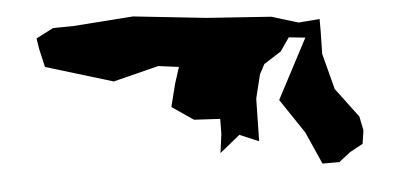

```mathematica
Graphics[Polygon[are1]]
```

```mathematica
llg=Graphics[{GrayLevel[.7],Polygon[are2],Inset[cull,{700,500},{695,500},1360]}]
```

-Graphics-
-Graphics-

```mathematica
λ=Vertices/Area[Polygon[are1]]
```

0.000397094

```mathematica
ω=Vertices/Area[Polygon[are2]]
```

0.000331019

```mathematica
Area[Polygon[are1*√λ]]
```

153.

```mathematica
coord1
```

{{66.0743,627.026},{1006.43,644.876},{193.743,653.904},{131.029,600.149},{187.024,604.628},{218.381,573.271},{256.458,575.511},{337.091,564.312},{370.688,506.077},{473.719,564.312},{489.398,586.71},{529.715,568.791},{556.592,566.552},{545.393,577.751},{547.633,604.628},{534.194,676.302},{496.118,615.827},{131.029,712.139},{211.662,721.098},{63.8345,669.583},{195.983,696.46},{899.283,539.674},{247.499,714.379},{267.657,703.18},{419.964,680.782},{458.041,694.221},{451.321,759.175},{637.225,564.312},{558.832,696.46},{596.909,651.664},{590.189,723.338},{621.547,707.659},{686.501,703.18},{659.624,629.266},{746.976,691.981},{746.976,734.537},{746.976,750.216},{935.12,698.7},{982.421,706.235},{1015.75,725.578},{1183.74,703.18},{1179.26,716.619},{1192.7,736.777},{1206.14,747.976},{1174.78,689.741},{1150.14,678.542},{1154.62,539.674},{1212.86,559.832},{1150.14,456.801},{1123.26,472.48},{1091.91,472.48},{1065.03,468.},{1065.12,732.913},{1224.06,526.235},{1219.58,452.321},{1266.61,468.},{1228.53,389.607},{930.64,577.751},{1241.97,268.657},{926.161,559.832},{1208.38,196.983},{1212.86,170.106},{1277.81,201.463},{1284.53,170.106},{1322.61,264.177},{1331.57,214.902},{1380.84,241.779},{1383.08,295.535},{1365.16,353.77},{608.108,396.326},{699.94,351.53},{802.971,353.77},{953.075,608.86},{1009.1,600.857},{1049.12,623.533},{885.844,459.041},{865.686,459.041},{807.451,503.837},{467.,653.904},{1014.43,758.258},{1215.1,691.981},{652.946,588.852},{650.278,555.504},{1121.15,732.913},{901.523,577.751},{626.268,484.807},{683.626,495.478},{748.987,460.797},{692.963,598.189},{732.981,602.191},{690.296,532.828},{740.984,555.504},{786.337,518.155},{786.337,479.472},{1214.52,608.86},{912.722,564.312},{1058.45,692.896},{923.729,658.215},{846.362,247.372},{963.746,715.573},{813.015,282.054},{835.691,358.086},{834.329,635.986},{797.008,368.757},{870.165,622.547},{805.011,390.1},{883.712,439.454},{879.71,482.139},{899.719,392.768},{950.407,430.117},{857.034,454.127},{830.356,428.783},{830.356,490.143},{794.34,438.121},{839.693,512.819},{862.369,543.499},{831.69,542.165},{910.482,620.307},{786.337,387.432},{794.34,411.442},{890.324,602.388},{910.482,595.669},{843.695,578.181},{846.362,622.199},{977.085,591.52},{985.089,635.538},{142.228,674.062},{240.779,700.94},{995.595,727.818},{1044.87,420.964},{1331.57,311.213},{1152.38,291.055},{874.645,288.815},{955.278,257.458},{95.1918,548.633},{1020.23,741.257},{648.945,544.833},{644.943,528.826},{1085.13,678.223},{1042.45,695.564},{803.678,210.023},{857.034,387.432},{759.659,386.098},{778.333,402.105},{935.734,507.484},{945.071,538.163},{1033.11,622.199},{963.746,526.158},{938.402,566.175},{983.755,570.177},{943.738,615.53},{906.002,550.873},{546.602,674.966}}

```mathematica
scoord1=√ω*coord1
```

{{1.20215,11.4081},{18.3109,11.7328},{3.52495,11.8971},{2.38393,10.9191},{3.4027,11.0006},{3.97321,10.4301},{4.66598,10.4708},{6.13301,10.267},{6.74428,9.20752},{8.61882,10.267},{8.90407,10.6746},{9.63759,10.3485},{10.1266,10.3078},{9.92285,10.5116},{9.9636,11.0006},{9.71909,12.3046},{9.02633,11.2043},{2.38393,12.9566},{3.85096,13.1196},{1.1614,12.1823},{3.5657,12.6714},{16.3615,9.81879},{4.50298,12.9974},{4.86973,12.7936},{7.6408,12.3861},{8.33356,12.6306},{8.21131,13.8124},{11.5936,10.267},{10.1674,12.6714},{10.8601,11.8563},{10.7379,13.1604},{11.3084,12.8751},{12.4902,12.7936},{12.0011,11.4488},{13.5904,12.5899},{13.5904,13.3641},{13.5904,13.6494},{17.0135,12.7121},{17.8741,12.8492},{18.4805,13.2011},{21.5369,12.7936},{21.4554,13.0381},{21.6999,13.4049},{21.9444,13.6086},{21.3739,12.5491},{20.9256,12.3453},{21.0071,9.81879},{22.0666,10.1855},{20.9256,8.311},{20.4366,8.59626},{19.8661,8.59626},{19.3771,8.51476},{19.3788,13.3346},{22.2704,9.57428},{22.1889,8.2295},{23.0446,8.51476},{22.3519,7.08848},{16.932,10.5116},{22.5964,4.88793},{16.8505,10.1855},{21.9851,3.5839},{22.0666,3.09489},{23.2484,3.6654},{23.3706,3.09489},{24.0634,4.80643},{24.2264,3.90991},{25.1229,4.39892},{25.1637,5.37694},{24.8377,6.43646},{11.0639,7.21073},{12.7347,6.39571},{14.6092,6.43646},{17.3402,11.0776},{18.3595,10.9319},{19.0875,11.3445},{16.117,8.35176},{15.7502,8.35176},{14.6907,9.16677},{8.49657,11.8971},{18.4565,13.7957},{22.1074,12.5899},{11.8797,10.7135},{11.8311,10.1068},{20.3981,13.3346},{16.4022,10.5116},{11.3943,8.82055},{12.4378,9.0147},{13.627,8.38371},{12.6077,10.8834},{13.3358,10.9562},{12.5592,9.69423},{13.4814,10.1068},{14.3066,9.42727},{14.3066,8.72347},{22.0969,11.0776},{16.606,10.267},{19.2574,12.6065},{16.8063,11.9755},{15.3987,4.50067},{17.5343,13.0191},{14.7919,5.13167},{15.2045,6.515},{15.1797,11.5711},{14.5007,6.70915},{15.8317,11.3266},{14.6463,7.09745},{16.0782,7.9954},{16.0054,8.77201},{16.3694,7.14599},{17.2916,7.82552},{15.5928,8.26236},{15.1074,7.80125},{15.1074,8.91762},{14.4522,7.97113},{15.2773,9.3302},{15.6899,9.88838},{15.1317,9.86411},{16.5652,11.2858},{14.3066,7.04891},{14.4522,7.48575},{16.1985,10.9598},{16.5652,10.8376},{15.3501,10.5194},{15.3987,11.3203},{17.777,10.7621},{17.9226,11.5629},{2.58768,12.2638},{4.38072,12.7529},{18.1138,13.2419},{19.0103,7.65899},{24.2264,5.6622},{20.9663,5.29544},{15.9132,5.25469},{17.3803,4.68417},{1.73191,9.98179},{18.562,13.4864},{11.8069,9.91265},{11.734,9.62142},{19.7428,12.3395},{18.9662,12.655},{14.6221,3.82114},{15.5928,7.04891},{13.8212,7.02464},{14.1609,7.31587},{17.0247,9.23312},{17.1946,9.79131},{18.7963,11.3203},{17.5343,9.57289},{17.0732,10.301},{17.8984,10.3738},{17.1703,11.1989},{16.4837,10.0225},{9.94484,12.2803}}

```mathematica
Clear[Distance]
```

```mathematica
Distance[x_,y_,z_,w_]:=Sqrt[(x-y)^2+(z-w)^2]
```

```mathematica
scoord1[[1]]
```

{1.20215,11.4081}

```mathematica
scoord1[[107]]
```

{16.0782,7.9954}

```mathematica
√λ*{466.41035353535347,653.7386363636365}
```

{9.29426,13.0272}

```mathematica
Nearest[scoord1,√λ*{466.41035353535347,653.7386363636365}]
```

{{9.71909,12.3046}}

```mathematica
Position[scoord1,Flatten@Nearest[scoord1,√λ*{466.41035353535347,653.7386363636365}]]
```

{{16}}

```mathematica
EuclideanDistance[scoord1[[1]],scoord1[[79]]]
```

7.31079

```mathematica
scoord= √λ rcoord
```

{{1.31668,12.4949},{2.8342,13.4322},{3.86077,13.0305},{2.61104,11.9593},{3.72687,12.0486},{4.35173,11.4237},{5.11049,11.4683},{6.71729,11.2452},{7.38678,10.0847},{9.43991,11.2452},{9.75234,11.6915},{10.5557,11.3344},{11.0913,11.2898},{10.8682,11.513},{10.9128,12.0486},{10.645,13.4768},{9.88624,12.2717},{2.61104,14.1909},{4.21783,14.3695},{1.27204,13.3429},{3.9054,13.8785},{4.79806,13.9678},{4.93196,14.2356},{5.33366,14.0124},{8.36871,13.5661},{9.12747,13.8339},{8.99358,15.1282},{12.6981,11.2452},{11.136,13.8785},{11.8947,12.9859},{11.7608,14.4141},{12.3857,14.1017},{13.6801,14.0124},{13.1445,12.5395},{14.8851,13.7892},{14.8851,14.6373},{14.8851,14.9497},{18.6343,13.9231},{19.8394,14.5034},{20.2411,14.4587},{23.5886,14.0124},{23.4993,14.2802},{23.7671,14.6819},{24.0349,14.9051},{23.4101,13.7446},{22.9191,13.5214},{23.0084,10.7542},{24.1688,11.1559},{22.9191,9.10277},{22.3835,9.4152},{21.7587,9.4152},{21.2231,9.32593},{20.8214,8.38864},{24.392,10.4864},{24.3027,9.0135},{25.24,9.32593},{24.4813,7.76378},{26.5344,6.20162},{24.7491,5.35359},{22.9637,5.79992},{24.0796,3.92533},{24.1688,3.38973},{25.4632,4.01459},{25.5971,3.38973},{26.3559,5.26432},{26.5344,4.28239},{27.5163,4.81799},{27.561,5.88918},{27.2039,7.04965},{12.1179,7.89767},{13.9479,7.00501},{16.001,7.04965},{17.4292,5.75528},{19.036,5.13042},{1.89691,10.9327},{17.6524,9.1474},{17.2507,9.1474},{16.0902,10.0401},{9.30601,13.0305},{20.3304,14.7712},{24.2135,13.7892},{13.0114,11.7342},{12.9582,11.0696},{12.9317,10.857},{12.8519,10.538},{12.4798,9.66086},{13.6228,9.8735},{14.9252,9.1824},{13.8088,11.9202},{14.6063,12.},{13.7557,10.6178},{14.7657,11.0696},{15.6695,10.3254},{15.6695,9.55453},{24.202,12.1329},{21.6236,13.5151},{21.092,13.8075},{20.773,13.8607},{16.8656,4.92944},{16.0151,4.18517},{16.2011,5.62054},{16.653,7.13566},{17.0783,7.72044},{15.8821,7.34831},{15.1379,7.69386},{16.0416,7.7736},{17.6099,8.7571},{17.5302,9.60769},{17.9289,7.82677},{18.939,8.57103},{17.0783,9.04949},{16.5467,8.54445},{16.5467,9.76718},{15.829,8.73052},{16.7327,10.2191},{17.1846,10.8304},{16.5733,10.8038},{15.51,8.01283},{15.6695,7.72044},{15.829,8.1989},{18.6466,10.1127},{18.8326,10.7241},{16.8125,11.5215},{16.8656,12.3987},{19.4706,11.7873},{19.6301,12.6645},{20.0554,12.8506},{20.587,12.3987},{19.5769,14.0733},{21.2249,14.6049},{19.2048,10.4849},{18.6997,11.2823},{18.9921,12.1329},{20.1085,11.9734},{20.906,12.4253},{20.2148,15.11},{22.3413,14.6049},{19.6035,11.362},{18.8061,12.2658},{18.4073,13.1164},{19.2048,14.2594},{16.6258,12.6734},{17.34,12.4056},{18.1434,12.361},{17.7417,12.0039},{18.1434,11.87},{17.9202,10.7542},{18.5451,11.513},{18.4558,11.1559},{17.9648,11.513},{18.188,11.2452},{18.0541,10.9774},{10.8923,13.4502}}

```mathematica
muu//MatrixForm
```

(1)
 |  |  |  |

```mathematica
coord1[[15]]
coord1[[16]]
coord1[[17]]
```

{547.633,604.628}

{534.194,676.302}

{496.118,615.827}

```mathematica
avlength=0; 
edgecnt=0; 
For[i=1,i≤ 153,i++, If[  muu[[#,i]]>0,{ edgecnt+= muu[[#,i]]  ,avlength += muu[[#,i]]*EuclideanDistance[scoord1[[#]],scoord1[[i]]  ]}]]  &/@Table[y,{y,153}];
avlength/edgecnt
edgecnt
```

1.13932

588

```mathematica
scoord1[[1]]   

 scoord1[[3]]
```

{1.20215,11.4081}

{3.52495,11.8971}

```mathematica
EuclideanDistance[scoord1[[1]] , scoord1[[3]]]
```

2.37372

```mathematica
avlengthgl=0; 
edgecntgl=0; 
For[i=1,i≤ 126,i++, { edgecntgl+= muu[[#,i]],(*Print[  i,"  ", #,"   ", EuclideanDistance[scoord1[[#]],scoord1[[i]] ]]   ,*)avlengthgl +=    muu[[#,i]]*( EuclideanDistance[scoord1[[#]],scoord1[[i]] ])}   ]   &/@Table[y,{y,127,153}];
avlengthgl/edgecntgl
edgecntgl
```

1.16981

101

```mathematica
avlengthgg=0; 
edgecntgg=0; 
For[i=127,i≤ 153,i++, { edgecntgg+= muu[[#,i]],(*Print[  i,"  ", #,"   ", EuclideanDistance[scoord1[[#]],scoord1[[i]] ]]   ,*)avlengthgg +=    muu[[#,i]]*( EuclideanDistance[scoord1[[#]],scoord1[[i]] ])}    ] &/@Table[y,{y,127,153}];
avlengthgg/edgecntgg
edgecntgg
```

0.941033

22

```mathematica
avlengthll=0; 
edgecntll=0; 
For[i=1,i≤ 126,i++, { edgecntll+= muu[[#,i]],(*Print[  i,"  ", #,"   ", EuclideanDistance[scoord1[[#]],scoord1[[i]] ]]   ,*)avlengthll +=    muu[[#,i]]*( EuclideanDistance[scoord1[[#]],scoord1[[i]] ])}    ] &/@Table[y,{y,1,126}];
avlengthll/edgecntll
edgecntll
```

1.13438

364

```mathematica
376+22+2*95
```

588

```mathematica
?Map
```

RowBox[{"Map", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"]}], "]"}] or RowBox[{StyleBox["f", "TI"], "/@", StyleBox["expr", "TI"]}] applies StyleBox["f", "TI"] to each element on the first level in StyleBox["expr", "TI"]. 
RowBox[{"Map", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] applies StyleBox["f", "TI"] to parts of StyleBox["expr", "TI"] specified by StyleBox["levelspec", "TI"]. 
RowBox[{"Map", "[", StyleBox["f", "TI"], "]"}] represents an operator form of Map that can be applied to an expression.

```mathematica
iwmuu=muu;
For[i=1,i≤ 153,i++, If[#≠ i,iwmuu[[i,#]]=muu[[i,#]]*(EuclideanDistance[scoord1[[#]],scoord1[[i]] ])    ]    ] &/@Table[y,{y,1,153}];
```

```mathematica
iwmuu  //MatrixForm
```

(1)
 |  |  |  |

```mathematica
For[i=1,i≤ 153,i++, If[iwmuu[[i,#]] ≥ 8,Print[":",i,    ":",#]    ]] &/@Table[y,{y,1,153}];
```

:135:28

:49:41

:41:49

:28:135

```mathematica
coord1[[135]]
coord1[[28]]
coord1[[49]]
coord1[[41]]
```

{95.1918,548.633}

{637.225,564.312}

{1150.14,456.801}

{1183.74,703.18}

```mathematica
i2
```

-Graphics-

```mathematica
wmuu=muu;
For[i=1,i≤ 153,i++, If[#≠ i,wmuu[[i,#]]=muu[[i,#]]/(EuclideanDistance[scoord1[[#]],scoord1[[i]] ])    ]    ] &/@Table[y,{y,1,153}];
```

```mathematica
wmuu//MatrixForm
```

(1)
 |  |  |  |

```mathematica
wmuu[[22,152]]
```

8.41692

```mathematica
muu//MatrixForm
```

(1)
 |  |  |  |

```mathematica
R=0;
Rgg=0; 
Rll=0; 
Rlg=0; 
For[i=1,i≤ 153,i++, If[wmuu[[#,i]] ≠ 0,R+=1/wmuu[[#,i]]    ]    ] &/@Table[y,{y,1,153}];
For[i=127,i≤ 153,i++, If[wmuu[[#,i]] ≠ 0,Rgg+=1/wmuu[[#,i]]    ]    ] &/@Table[y,{y,127,153}];
For[i=1,i≤ 126,i++, If[wmuu[[#,i]] ≠ 0,Rll+=1/wmuu[[#,i]]    ]    ] &/@Table[y,{y,1,126}];
For[i=1,i≤ 127,i++, If[wmuu[[#,i]] ≠ 0,Rlg+=1/wmuu[[#,i]]    ]    ] &/@Table[y,{y,127,153}];
Rgg
Rlg
Rll
R/2
```

8.01997

63.577

264.911

200.042

```mathematica
Rlg+Rll/2+Rgg/2
```

200.042

```mathematica
lledges=0; 
For[i=1,i≤ 126,i++, If[muu[[#,i]] > 0,lledges+=Sign[muu[[#,i]] ]  ]    ] &/@Table[y,{y,1,126}];
lledges
lgedges=0; 
For[i=1,i≤ 126,i++, If[muu[[#,i]] > 0,lgedges+=Sign[muu[[#,i]] ]  ]    ] &/@Table[y,{y,127,153}];
lgedges
ggedges=0; 
For[i=127,i≤ 153,i++, If[muu[[#,i]] > 0,ggedges+=Sign[muu[[#,i]] ]  ]    ] &/@Table[y,{y,127,153}];
ggedges
edgess= lledges+ggedges+2*lgedges
```

252

61

14

388

```mathematica
amuu = muu;
For[i=1,i≤ 153,i++, amuu[[i,#]]=Sign[muu[[i,#]]  ]     ] &/@Table[y,{y,1,153}];
amuu //MatrixForm
```

(1)
 |  |  |  |

```mathematica
ki =0; 
si =0 ; 
clusteringi = 0;
For[j=1,j≤  153,j++,{ki = Total[amuu[[#]]],si  = Total[wmuu[[#]]],If[ki>1,For[h=1,h≤ 153,h++,clusteringi +=(.5)/(si(ki-1))*(wmuu[[#,h]]+wmuu[[#,j]])* amuu[[#,h]]*amuu[[#,j]]*amuu[[h,j]] ]]}]&/@Table[y,{y,1,153}];
clusteringi/119
```

0.0707938

```mathematica
ggedges/edgess //N
```

0.0360825

```mathematica
values ={{"  ","MDG","FLG"},{"nodes",153,84},{"number ofgenerators",ng,31},{"number ofloads",nl,53},{"power lines",edgecnt/2,200},{"<k>",kk,4.76},{"<k_g>",kg,4.48},{"<k_l>",kl,4.93},{"<ℓ>",avlength/edgecnt,1.09},{"<ℓ_gg>",avlengthgg/edgecntgg,0.71},{"<ℓ_gl>",avlengthgl/edgecntgl,1.02},{"<ℓ_ll>",avlengthll/edgecntll,1.27},{"e_gg",edgecntgg/edgecnt,0.085},{"e_gl",edgecntgl/edgecnt,0.2625},{"e_ll",edgecntll/edgecnt,0.39},{"<R_gg>",Rgg/ggedges,0.57},{"<R_gl>",Rlg/lgedges,0.96},{"<R_ll>",Rll/lledges,1.20},{"R",R/2,139.78},{"<C^ω>",clusteringi/119,0.21},{"<M_ex>",100,63},{"<d_B>","",1.37}}//N
```

{{  ,MDG,FLG},{nodes,153.,84.},{number ofgenerators,27.,31.},{number ofloads,126.,53.},{power lines,294.,200.},{<k>,3.84314,4.76},{<k_g>,4.55556,4.48},{<k_l>,3.69048,4.93},{<ℓ>,1.13932,1.09},{<ℓ_gg>,0.941033,0.71},{<ℓ_gl>,1.16981,1.02},{<ℓ_ll>,1.13438,1.27},{e_gg,0.037415,0.085},{e_gl,0.171769,0.2625},{e_ll,0.619048,0.39},{<R_gg>,0.572855,0.57},{<R_gl>,1.04225,0.96},{<R_ll>,1.05123,1.2},{R,200.042,139.78},{<C^ω>,0.,0.21},{<M_ex>,100.,63.},{<d_B>,,1.37}}

```mathematica
TableForm[values]
```

| MDG | FLG
nodes | 153. | 84.
number ofgenerators | 27. | 31.
number ofloads | 126. | 53.
power lines | 294. | 200.
<k> | 3.84314 | 4.76
<k_g> | 4.55556 | 4.48
<k_l> | 3.69048 | 4.93
<ℓ> | 1.13932 | 1.09
<ℓ_gg> | 0.941033 | 0.71
<ℓ_gl> | 1.16981 | 1.02
<ℓ_ll> | 1.13438 | 1.27
e_gg | 0.037415 | 0.085
e_gl | 0.171769 | 0.2625
e_ll | 0.619048 | 0.39
<R_gg> | 0.572855 | 0.57
<R_gl> | 1.04225 | 0.96
<R_ll> | 1.05123 | 1.2
R | 200.042 | 139.78
<C^ω> | 0. | 0.21
<M_ex> | 100. | 63.
<d_B> |  | 1.37

```mathematica
muu //MatrixForm
```

(1)
 |  |  |  |

```mathematica
edgei =0; 
vertexstrength =0 ; 
line=0; 
clusteringi = 0;
{line+= Total[muu[[#]]],edgei += Total[amuu[[#]]],vertexstrength  +=Total[ wmuu[[#]]]} &/@Table[y,{y,1,153}];
edgei/2
line/2
vertexstrength
```

194

294

824.851

```mathematica
Total
```

```mathematica
?Sign
```

RowBox[{"Sign", "[", StyleBox["x", "TI"], "]"}] gives RowBox[{"-", "1"}], 0, or 1 depending on whether StyleBox["x", "TI"] is negative, zero, or positive.

```mathematica
edgessm=0; 
linessm=0; 
linessm+=Total[muu[[#]]]&/@Table[y,{y,1,153}];
edgessm+=Total[amuu[[#]]]&/@Table[y,{y,1,153}];
linessm/2
edgessm/2
```

294

194

```mathematica
294-194
```

```mathematica
100
```

100

```mathematica
edgessm=0; 
For[j=1,j≤  153,j++,If[Total[amuu[[j]]]==1,edgessm++]]
edgessm
```

34

```mathematica
153-34
```

119

```mathematica
0.07079377134119474*153/119
```

0.0910206